## Linear noise matrices for generalized 3-component system

```mathematica
Mmatr=Simplify[{1/Subscript[τ, x]{1-Subscript[h, x],-Subscript[h, 1],-Subscript[h, 2]},1/Subscript[τ, 1]{0,1,E1}, 1/Subscript[τ, 2]{-1,E2,1}}];
MatrixForm[Mmatr]
```

((1-h_x)/τ_x | -h_1/τ_x | -h_2/τ_x
0 | 1/τ_1 | E1/τ_1
-1/τ_2 | E2/τ_2 | 1/τ_2)

```mathematica
Dmatr=Simplify[{{2/(Subscript[τ, x]⟨x⟩),0, 0},{0,2/(Subscript[τ, 1]⟨Subscript[z, 1]⟩),1/2(E1/(Subscript[τ, 1]⟨Subscript[z, 2]⟩)+E2/(Subscript[τ, 2]⟨Subscript[z, 1]⟩))}, {0,1/2(E1/(Subscript[τ, 1]⟨Subscript[z, 2]⟩)+E2/(Subscript[τ, 2]⟨Subscript[z, 1]⟩)),2/(Subscript[τ, 2]⟨Subscript[z, 2]⟩)}}];
MatrixForm[Dmatr]
```

(2/(⟨x⟩ τ_x) | 0 | 0
0 | 2/(⟨z_1⟩ τ_1) | 1/2 (E1/(⟨z_2⟩ τ_1)+E2/(⟨z_1⟩ τ_2))
0 | 1/2 (E1/(⟨z_2⟩ τ_1)+E2/(⟨z_1⟩ τ_2)) | 2/(⟨z_2⟩ τ_2))

```mathematica
ETAmatr={{Subscript[η, xx],Subscript[η, x1], Subscript[η, x2]},{Subscript[η, x1],Subscript[η, 11], Subscript[η, 12]},{Subscript[η, x2],Subscript[η, 12], Subscript[η, 22]}};
MatrixForm[ETAmatr]
```

(η_xx | η_x1 | η_x2
η_x1 | η_11 | η_12
η_x2 | η_12 | η_22)

## Derivation of main text equation 6

```mathematica
MmatrIRA = Mmatr/.E1->1/.E2->1/.Subscript[h, 1]->1/.Subscript[h, x]->0/.Subscript[h, 2]->0;
MatrixForm[MmatrIRA]
```

(1/τ_x | -1/τ_x | 0
0 | 1/τ_1 | 1/τ_1
-1/τ_2 | 1/τ_2 | 1/τ_2)

```mathematica
DmatrIRA = Dmatr/.E1->1/.E2->1;
MatrixForm[DmatrIRA]
```

(2/(⟨x⟩ τ_x) | 0 | 0
0 | 2/(⟨z_1⟩ τ_1) | 1/2 (1/(⟨z_2⟩ τ_1)+1/(⟨z_1⟩ τ_2))
0 | 1/2 (1/(⟨z_2⟩ τ_1)+1/(⟨z_1⟩ τ_2)) | 2/(⟨z_2⟩ τ_2))

```mathematica
covsIRA=Solve[MmatrIRA.ETAmatr+Transpose[MmatrIRA.ETAmatr]==DmatrIRA,Flatten[ETAmatr]][[1]];
```

```mathematica
etaxxIRA= Collect[(Subscript[η, xx]/.covsIRA), {1/⟨x⟩,1/⟨Subscript[z, 1]⟩,1/⟨Subscript[z, 2]⟩}]
```

-(-τ_1^2 τ_2-2 τ_1 τ_2^2-τ_1^2 τ_x-τ_1 τ_2 τ_x)/(2 ⟨z_1⟩ (τ_1^2 τ_2+τ_1 τ_2^2+τ_1^2 τ_x+τ_1 τ_2 τ_x+τ_2^2 τ_x))-(-2 τ_1^2 τ_2-2 τ_1 τ_2^2-2 τ_1^2 τ_x-4 τ_1 τ_2 τ_x-2 τ_2^2 τ_x)/(2 ⟨x⟩ (τ_1^2 τ_2+τ_1 τ_2^2+τ_1^2 τ_x+τ_1 τ_2 τ_x+τ_2^2 τ_x))-(-τ_1 τ_2^2-τ_1 τ_2 τ_x-τ_2^2 τ_x)/(2 ⟨z_2⟩ (τ_1^2 τ_2+τ_1 τ_2^2+τ_1^2 τ_x+τ_1 τ_2 τ_x+τ_2^2 τ_x))

```mathematica
canboundIRA = Simplify[Limit[(etaxxIRA/.Subscript[τ, 2]->⟨Subscript[z, 2]⟩/μ),⟨Subscript[z, 2]⟩->∞]]
```

1/⟨x⟩+τ_1/(⟨z_1⟩ (τ_1+τ_x))

```mathematica
Reduce[etaxxIRA < canboundIRA && ⟨x⟩>0 && ⟨Subscript[z, 1]⟩>0&&⟨Subscript[z, 2]⟩>0&&Subscript[τ, x]>0&&Subscript[τ, 1]==⟨Subscript[z, 1]⟩/μ&&Subscript[τ, 2]==⟨Subscript[z, 2]⟩/μ&&μ>0&&etaxxIRA>0]
```

False

## Linear noise analysis of idealized reference-actuated antithetic integral feedback system with additional negative feedback input

### Linear noise for reference-actuated AIF system with negative self-feedback on the controlled species X

```mathematica
MmatrNFBaif = Mmatr/.E1->1/.E2->1/.Subscript[h, 1]->1/.Subscript[h, 2]->0;
MatrixForm[MmatrNFBaif]
```

((1-h_x)/τ_x | -1/τ_x | 0
0 | 1/τ_1 | 1/τ_1
-1/τ_2 | 1/τ_2 | 1/τ_2)

```mathematica
DmatrNFBaif= Dmatr/.E1->1/.E2->1;
MatrixForm[DmatrNFBaif]
```

(2/(⟨x⟩ τ_x) | 0 | 0
0 | 2/(⟨z_1⟩ τ_1) | 1/2 (1/(⟨z_2⟩ τ_1)+1/(⟨z_1⟩ τ_2))
0 | 1/2 (1/(⟨z_2⟩ τ_1)+1/(⟨z_1⟩ τ_2)) | 2/(⟨z_2⟩ τ_2))

```mathematica
covsNFBaif=Solve[MmatrNFBaif.ETAmatr+Transpose[MmatrNFBaif.ETAmatr]==DmatrNFBaif,Flatten[ETAmatr]][[1]];
```

```mathematica
etaxxNFBaif= Collect[(Subscript[η, xx]/.covsNFBaif), {1/⟨x⟩,1/⟨Subscript[z, 1]⟩,1/⟨Subscript[z, 2]⟩}]
```

-(-τ_1^2 τ_2+h_x τ_1^2 τ_2-2 τ_1 τ_2^2-τ_1^2 τ_x-τ_1 τ_2 τ_x)/(2 ⟨z_1⟩ (τ_1^2 τ_2-2 h_x τ_1^2 τ_2+h_x^2 τ_1^2 τ_2+τ_1 τ_2^2-2 h_x τ_1 τ_2^2+h_x^2 τ_1 τ_2^2+τ_1^2 τ_x-h_x τ_1^2 τ_x+τ_1 τ_2 τ_x-2 h_x τ_1 τ_2 τ_x+τ_2^2 τ_x-h_x τ_2^2 τ_x))-(-2 τ_1^2 τ_2+2 h_x τ_1^2 τ_2-2 τ_1 τ_2^2+2 h_x τ_1 τ_2^2-2 τ_1^2 τ_x-4 τ_1 τ_2 τ_x-2 τ_2^2 τ_x)/(2 ⟨x⟩ (τ_1^2 τ_2-2 h_x τ_1^2 τ_2+h_x^2 τ_1^2 τ_2+τ_1 τ_2^2-2 h_x τ_1 τ_2^2+h_x^2 τ_1 τ_2^2+τ_1^2 τ_x-h_x τ_1^2 τ_x+τ_1 τ_2 τ_x-2 h_x τ_1 τ_2 τ_x+τ_2^2 τ_x-h_x τ_2^2 τ_x))-(-τ_1 τ_2^2+h_x τ_1 τ_2^2-τ_1 τ_2 τ_x-τ_2^2 τ_x)/(2 ⟨z_2⟩ (τ_1^2 τ_2-2 h_x τ_1^2 τ_2+h_x^2 τ_1^2 τ_2+τ_1 τ_2^2-2 h_x τ_1 τ_2^2+h_x^2 τ_1 τ_2^2+τ_1^2 τ_x-h_x τ_1^2 τ_x+τ_1 τ_2 τ_x-2 h_x τ_1 τ_2 τ_x+τ_2^2 τ_x-h_x τ_2^2 τ_x))

### Linear noise for system with ONLY negative self-feedback on the controlled species X (no AIF input)

```mathematica
etaxxNFB =(Subscript[η, xx]/. Solve[(1-Subscript[h, x])/Subscript[τ, x]*Subscript[η, xx] + Subscript[η, xx]*(1-Subscript[h, x])/Subscript[τ, x] == 2/(⟨x⟩ Subscript[τ, x]),  Subscript[η, xx]])[[1]]
```

-1/(⟨x⟩ (-1+h_x))

```mathematica
Simplify[Limit[(etaxxNFBaif/.Subscript[τ, 1]->⟨Subscript[z, 1]⟩/μ/.Subscript[τ, 2]->⟨Subscript[z, 2]⟩/μ),{⟨Subscript[z, 1]⟩->∞,⟨Subscript[z, 2]⟩->∞}]]
```

1/(⟨x⟩-⟨x⟩ h_x)

### Verify physical solutions for the system with both AIF and negative self-feedback are bounded from below by the solution for the system with just negative self-feedback

```mathematica
Reduce[etaxxNFBaif < etaxxNFB && ⟨x⟩>0 && ⟨Subscript[z, 1]⟩>0&&⟨Subscript[z, 2]⟩>0&&Subscript[τ, x]>0&&Subscript[τ, 1]==⟨Subscript[z, 1]⟩/μ&&Subscript[τ, 2]==⟨Subscript[z, 2]⟩/μ&&μ>0&&etaxxNFBaif>0&&Subscript[h, x]<0]
```

False

## Derivation of approximate sensitivity coefficient for the reference-actuated system with control species dilution

### Linear noise approximation

```mathematica
MmatrRA = Mmatr/.Subscript[h, 1]->1/.Subscript[h, x]->0/.Subscript[h, 2]->0;
MatrixForm[MmatrRA]
```

(1/τ_x | -1/τ_x | 0
0 | 1/τ_1 | E1/τ_1
-1/τ_2 | E2/τ_2 | 1/τ_2)

```mathematica
DmatrRA = Dmatr;
MatrixForm[DmatrRA]
```

(2/(⟨x⟩ τ_x) | 0 | 0
0 | 2/(⟨z_1⟩ τ_1) | 1/2 (E1/(⟨z_2⟩ τ_1)+E2/(⟨z_1⟩ τ_2))
0 | 1/2 (E1/(⟨z_2⟩ τ_1)+E2/(⟨z_1⟩ τ_2)) | 2/(⟨z_2⟩ τ_2))

```mathematica
covsRA=Solve[MmatrRA.ETAmatr+Transpose[MmatrRA.ETAmatr]==DmatrRA,Flatten[ETAmatr]][[1]];
```

```mathematica
etaxxRA= Collect[(Subscript[η, xx]/.covsRA), {1/⟨x⟩,1/⟨Subscript[z, 1]⟩,1/⟨Subscript[z, 2]⟩}]
```

-(2 τ_1^2 τ_2-E1 E2 τ_1^2 τ_2+2 τ_1 τ_2^2+2 E1 τ_1 τ_2^2-2 E1 E2 τ_1 τ_2^2+2 τ_1^2 τ_x-E1 E2 τ_1^2 τ_x+2 τ_1 τ_2 τ_x-E1 E2 τ_1 τ_2 τ_x)/(2 (-1-E1+E1 E2) ⟨z_1⟩ (τ_1^2 τ_2+τ_1 τ_2^2+τ_1^2 τ_x+2 τ_1 τ_2 τ_x-E1 τ_1 τ_2 τ_x+τ_2^2 τ_x+τ_1 τ_x^2-E1 E2 τ_1 τ_x^2+τ_2 τ_x^2-E1 E2 τ_2 τ_x^2))-(E1^2 τ_1 τ_2^2+E1^2 τ_1 τ_2 τ_x+E1^2 τ_2^2 τ_x)/(2 (-1-E1+E1 E2) ⟨z_2⟩ (τ_1^2 τ_2+τ_1 τ_2^2+τ_1^2 τ_x+2 τ_1 τ_2 τ_x-E1 τ_1 τ_2 τ_x+τ_2^2 τ_x+τ_1 τ_x^2-E1 E2 τ_1 τ_x^2+τ_2 τ_x^2-E1 E2 τ_2 τ_x^2))-(2 τ_1^2 τ_2+2 E1 τ_1^2 τ_2-2 E1 E2 τ_1^2 τ_2+2 τ_1 τ_2^2+2 E1 τ_1 τ_2^2-2 E1 E2 τ_1 τ_2^2+2 τ_1^2 τ_x+2 E1 τ_1^2 τ_x-2 E1 E2 τ_1^2 τ_x+4 τ_1 τ_2 τ_x+2 E1 τ_1 τ_2 τ_x-4 E1 E2 τ_1 τ_2 τ_x+2 E1^2 E2 τ_1 τ_2 τ_x+2 τ_2^2 τ_x+2 E1 τ_2^2 τ_x-2 E1 E2 τ_2^2 τ_x+2 τ_1 τ_x^2-4 E1 E2 τ_1 τ_x^2+2 E1^2 E2^2 τ_1 τ_x^2+2 τ_2 τ_x^2-4 E1 E2 τ_2 τ_x^2+2 E1^2 E2^2 τ_2 τ_x^2)/(2 (-1-E1+E1 E2) ⟨x⟩ (τ_1^2 τ_2+τ_1 τ_2^2+τ_1^2 τ_x+2 τ_1 τ_2 τ_x-E1 τ_1 τ_2 τ_x+τ_2^2 τ_x+τ_1 τ_x^2-E1 E2 τ_1 τ_x^2+τ_2 τ_x^2-E1 E2 τ_2 τ_x^2))

```mathematica
eta12RA= Collect[(Subscript[η, 12]/.covsRA), {1/⟨x⟩,1/⟨Subscript[z, 1]⟩,1/⟨Subscript[z, 2]⟩}]
```

(-2 τ_1^2 τ_2+E2 τ_1^2 τ_2-2 τ_1^2 τ_x+E2 τ_1^2 τ_x+2 E1 τ_1 τ_2 τ_x+E2 τ_1 τ_2 τ_x-2 E1 E2 τ_1 τ_2 τ_x+E2 τ_1 τ_x^2+E1 E2 τ_1 τ_x^2-E1 E2^2 τ_1 τ_x^2)/(2 (-1-E1+E1 E2) ⟨z_1⟩ (τ_1^2 τ_2+τ_1 τ_2^2+τ_1^2 τ_x+2 τ_1 τ_2 τ_x-E1 τ_1 τ_2 τ_x+τ_2^2 τ_x+τ_1 τ_x^2-E1 E2 τ_1 τ_x^2+τ_2 τ_x^2-E1 E2 τ_2 τ_x^2))+(2 E1 τ_1 τ_2 τ_x+2 E1 τ_1 τ_x^2+2 E1 τ_2 τ_x^2)/(2 (-1-E1+E1 E2) ⟨x⟩ (τ_1^2 τ_2+τ_1 τ_2^2+τ_1^2 τ_x+2 τ_1 τ_2 τ_x-E1 τ_1 τ_2 τ_x+τ_2^2 τ_x+τ_1 τ_x^2-E1 E2 τ_1 τ_x^2+τ_2 τ_x^2-E1 E2 τ_2 τ_x^2))+(E1 τ_1 τ_2^2+E1 τ_1 τ_2 τ_x+E1 τ_2^2 τ_x+E1 τ_2 τ_x^2+E1^2 τ_2 τ_x^2-E1^2 E2 τ_2 τ_x^2)/(2 (-1-E1+E1 E2) ⟨z_2⟩ (τ_1^2 τ_2+τ_1 τ_2^2+τ_1^2 τ_x+2 τ_1 τ_2 τ_x-E1 τ_1 τ_2 τ_x+τ_2^2 τ_x+τ_1 τ_x^2-E1 E2 τ_1 τ_x^2+τ_2 τ_x^2-E1 E2 τ_2 τ_x^2))

### Self-consistent expressions for averages and lifetimes in terms the flux ratio parameters E_1 and E_2

```mathematica
Xavg =μ/θ*E1/E2;
Z1avg = μ/Subscript[β, 1]*(1-E1);
Z2avg = μ/Subscript[β, 2]*E1/E2*(1-E2);
Z1Z2avg = μ/γ*E1;
Tau1 = (1-E1)/Subscript[β, 1];
Tau2 = (1-E2)/Subscript[β, 2];
```

```mathematica
Reduce[μ==γ*Z1Z2avg + Subscript[β, 1]*Z1avg&&θ*Xavg==γ*Z1Z2avg + Subscript[β, 2]*Z2avg && Tau1 == Z1avg/μ&&Tau2== Z2avg/(θ*Xavg)&&E1 ==(γ*Z1Z2avg)/μ&&E2 ==(γ*Z1Z2avg)/(θ*Xavg)]
```

True

### Make substitutions and solve for the approximate sensitivity coefficient

```mathematica
eta12identity[bx_] = Simplify[Z1Z2avg/(Z1avg*Z2avg)-1]/.E1->E1[bx]/.E2->E2[bx] (* let bx be a stand-in for Subscript[β, x] *)
```

-1+(E2[bx] β_1 β_2)/(γ μ (-1+E1[bx]) (-1+E2[bx]))

```mathematica
eta12LNA[bx_] = Simplify[eta12RA/.Subscript[τ, x]->(1/bx)/.Subscript[τ, 1]->Tau1/.Subscript[τ, 2]->Tau2/.⟨x⟩->Xavg/.⟨Subscript[z, 1]⟩->Z1avg/.⟨Subscript[z, 2]⟩->Z2avg/.E1->E1[bx]/.E2->E2[bx]]
```

(β_1 β_2 ((bx+θ) E2[bx]^2 (bx+β_1)+bx (bx+β_2)-E2[bx] (bx (2 bx+θ)+(bx+θ) β_2+β_1 (bx+θ+β_2))-E1[bx] (E2[bx]^2 (bx (bx+θ)+β_1 (bx-β_2))+bx (bx+β_1+β_2)-E2[bx] (bx (2 bx+θ)+β_1 (2 bx-β_2)+(bx+θ) β_2))))/(μ (-1+E1[bx] (-1+E2[bx])) (bx (-1+E1[bx])^2 (-bx+bx E2[bx]-β_2) β_2-(-1+E2[bx]) β_1^2 (-bx-β_2+E2[bx] (bx+E1[bx] β_2))+(-1+E1[bx]) β_1 (bx^2+bx^2 E2[bx]^2-bx (-2+E1[bx]) β_2+β_2^2-E2[bx] (2 bx^2-bx (-2+E1[bx]) β_2+E1[bx] β_2^2))))

```mathematica
eta12RA
```

(-2 τ_1^2 τ_2+E2 τ_1^2 τ_2-2 τ_1^2 τ_x+E2 τ_1^2 τ_x+2 E1 τ_1 τ_2 τ_x+E2 τ_1 τ_2 τ_x-2 E1 E2 τ_1 τ_2 τ_x+E2 τ_1 τ_x^2+E1 E2 τ_1 τ_x^2-E1 E2^2 τ_1 τ_x^2)/(2 (-1-E1+E1 E2) ⟨z_1⟩ (τ_1^2 τ_2+τ_1 τ_2^2+τ_1^2 τ_x+2 τ_1 τ_2 τ_x-E1 τ_1 τ_2 τ_x+τ_2^2 τ_x+τ_1 τ_x^2-E1 E2 τ_1 τ_x^2+τ_2 τ_x^2-E1 E2 τ_2 τ_x^2))+(2 E1 τ_1 τ_2 τ_x+2 E1 τ_1 τ_x^2+2 E1 τ_2 τ_x^2)/(2 (-1-E1+E1 E2) ⟨x⟩ (τ_1^2 τ_2+τ_1 τ_2^2+τ_1^2 τ_x+2 τ_1 τ_2 τ_x-E1 τ_1 τ_2 τ_x+τ_2^2 τ_x+τ_1 τ_x^2-E1 E2 τ_1 τ_x^2+τ_2 τ_x^2-E1 E2 τ_2 τ_x^2))+(E1 τ_1 τ_2^2+E1 τ_1 τ_2 τ_x+E1 τ_2^2 τ_x+E1 τ_2 τ_x^2+E1^2 τ_2 τ_x^2-E1^2 E2 τ_2 τ_x^2)/(2 (-1-E1+E1 E2) ⟨z_2⟩ (τ_1^2 τ_2+τ_1 τ_2^2+τ_1^2 τ_x+2 τ_1 τ_2 τ_x-E1 τ_1 τ_2 τ_x+τ_2^2 τ_x+τ_1 τ_x^2-E1 E2 τ_1 τ_x^2+τ_2 τ_x^2-E1 E2 τ_2 τ_x^2))

```mathematica
X[bx_] = Xavg/.E1->E1[bx]/.E2->E2[bx];
Z1[bx_] = Z1avg/.E1->E1[bx]/.E2->E2[bx];
```

```mathematica
dE12dTapprox = Solve[D[k*Z1[bx],bx] == D[bx*X[bx],bx]&&D[eta12LNA[bx], bx]==D[eta12identity[bx] ,bx],{E1'[bx],E2'[bx]}]
```

{{E1'[bx]→-((bx μ 1 (-1/1+28+1/1))/(θ E2[bx]^2)+(μ E1[bx] (1))/(θ E2[bx]))/(-(-(bx μ)/(θ E2[bx])-(k μ)/β_1) (-(β_1 β_2)/(γ μ (-1+E1[bx]) (-1+E2[bx]))+16)+(bx μ E1[bx] (1))/(θ (E212])^2)),E2'[bx]→(E2[bx] (1))/1}}
 |  |  |  |

```mathematica
kConsistency = k/.Solve[k*Z1avg == bx*Xavg, k][[1]] (* solve for self-consistent value of k *)
```

-(bx E1 β_1)/((-1+E1) E2 θ)

```mathematica
Sapprox[E1_,E2_,μ_,θ_,b1_,b2_,γ_,bx_] = bx/X[bx]*D[X[bx],bx]/.E1'[bx]->(E1'[bx]/.dE12dTapprox[[1]])/.E2'[bx]->(E2'[bx]/.dE12dTapprox[[1]])/.E1[bx]->E1/.E2[bx]->E2/.k->kConsistency/.Subscript[β, 1]->b1/.Subscript[β, 2]->b2
```

(bx E2 θ (-(E1 (3031+(b1^2 4 θ)/1) μ)/(E2 θ (1))-(μ (1))/(E2 θ (1-1))))/(E1 μ)
 |  |  |  |

```mathematica
Limit[Sapprox[E1,E2,μ,θ,b1,b2,γ,bx],E2->1] (* we take S in absolute value --> 1-Subscript[E, 1], since E1 ≤ 1*)
```

-1+E1

```mathematica
Clear[SapproxSPtracking]
SapproxSPtracking[e_,θ_,b1_,b2_,γ_,bx_]=Simplify[Sapprox[e,e,μ,θ,b1,b2,γ,bx]]
```

-(((-1+e) (b1^4 (1+e) (b2+bx+b2 e)^2 (1+e-e^2)^2+b2 bx (b2+bx-bx e)^2 (b2 bx (1+e) (1+e-e^2)^2+bx (-1+e)^3 (-1+2 e) γ+(1+2 e^2-6 e^3+3 e^4) γ θ)+b1^2 (b2^4 (1+e)^3 (1+e-e^2)^2-b2^3 (1+e-e^2)^2 (2 bx (-3+e) (1+e)^2-(1+e+2 e^2) γ)+bx^2 (-1+e)^2 (bx^2 (1+e) (1+e-e^2)^2+bx (5-2 e+7 e^2-10 e^3+3 e^4) γ+2 (1+e+3 e^2-3 e^3) γ θ)-b2^2 (bx^2 (1+e-e^2)^2 (-10-6 e+7 e^2+3 e^3)+bx (-7+4 e-7 e^2+21 e^4-18 e^5+4 e^6) γ+2 (-1+e-2 e^2+5 e^4-3 e^5) γ θ)+b2 bx (-1+e) (2 bx^2 (-3-8 e+10 e^3-4 e^5+e^6)+bx (-11+8 e-15 e^2+14 e^3-2 e^5) γ-(4+8 e^2-10 e^3+e^4+e^5) γ θ))+b1 (2 b2^4 bx (-1-2 e+e^3)^2+bx^3 (-1+e)^3 γ (bx (-1+e)^2 (-1+2 e)+(-1-e-3 e^2+3 e^3) θ)+b2 bx^2 (-1+e)^2 (2 bx^2 (1+e) (1+e-e^2)^2+bx (6-12 e+23 e^2-18 e^3+4 e^4) γ+(4+4 e+13 e^2-15 e^3+2 e^4) γ θ)+b2^2 bx (-1+e) (2 bx^2 (-3-8 e+10 e^3-4 e^5+e^6)+bx (-9+10 e-21 e^2+12 e^3+6 e^4-4 e^5) γ-(4+8 e^2-10 e^3+e^4+e^5) γ θ)+b2^3 (-2 bx^2 (1+e-e^2)^2 (-3-2 e+2 e^2+e^3)+bx (4-2 e+3 e^2+4 e^3-10 e^4+4 e^5) γ+(1-e+2 e^2-5 e^4+3 e^5) γ θ))+b1^3 (2 b2^3 (1+e)^3 (1+e-e^2)^2-b2^2 (1+e-e^2)^2 (2 bx (-3+e) (1+e)^2-(1+e+2 e^2) γ)-bx (-1+e) (2 bx^2 (1+e) (1+e-e^2)^2+bx (2-2 e+4 e^2-4 e^3+e^4) γ+(1+e+3 e^2-3 e^3) γ θ)+b2 (-2 bx^2 (1+e-e^2)^2 (-3-2 e+2 e^2+e^3)+bx (3-2 e+7 e^2+2 e^3-14 e^4+8 e^5-e^6) γ+(1-e+2 e^2-5 e^4+3 e^5) γ θ))))/(b1^4 (b2+bx+b2 e)^2 (-1-e+e^2)^3+b2 bx (b2+bx-bx e)^2 (b2 bx (-1-e+e^2)^3+(-1+e)^2 γ (bx (-1+3 e-5 e^2+2 e^3)+(-1-e-3 e^2+2 e^3) θ))+b1 (2 b2^4 bx (1+e) (-1-e+e^2)^3+bx^3 (-1+e)^3 γ (bx (-1+e)^2 (1-3 e+e^2)+(1+3 e^2-4 e^3+e^4) θ)+b2 bx^2 (-1+e)^2 (2 bx^2 (-1-e+e^2)^3+bx (-5+16 e-32 e^2+37 e^3-20 e^4+4 e^5) γ+2 (-2-5 e^2+11 e^3-6 e^4+e^5) γ θ)+b2^2 bx (-1+e) (2 bx^2 (-3+e) (-1-e+e^2)^3+bx (7-15 e+30 e^2-35 e^3+7 e^4+10 e^5-4 e^6) γ-2 (-2+e-4 e^2+10 e^3-4 e^4-2 e^5+e^6) γ θ)+b2^3 (-2 bx^2 (-1-e+e^2)^3 (-3+e+e^2)+bx (-3+4 e-6 e^2+3 e^3+12 e^4-14 e^5+4 e^6) γ+(-1+e-3 e^2+3 e^3+5 e^4-7 e^5+2 e^6) γ θ))+b1^3 (2 b2^3 (1+e)^2 (-1-e+e^2)^3-b2^2 (1+e-e^2)^2 (2 bx (3+5 e-2 e^2-3 e^3+e^4)+(1+e+2 e^2-e^3) γ)-bx (-1+e) (2 bx^2 (-1-e+e^2)^3+bx (-2+3 e-7 e^2+7 e^3-2 e^4) γ-(1+3 e^2-4 e^3+e^4) γ θ)+b2 (-2 bx^2 (-1-e+e^2)^3 (-3+e+e^2)-bx (3-2 e+9 e^2-6 e^3-13 e^4+17 e^5-7 e^6+e^7) γ+(-1+e-3 e^2+3 e^3+5 e^4-7 e^5+2 e^6) γ θ))+b1^2 (b2^4 (1+e)^2 (-1-e+e^2)^3-b2^3 (1+e-e^2)^2 (2 bx (3+5 e-2 e^2-3 e^3+e^4)+(1+e+e^2-2 e^3) γ)+bx^2 (-1+e)^2 (bx^2 (-1-e+e^2)^3+bx (-4+7 e-12 e^2+13 e^3-6 e^4+e^5) γ-2 (1+3 e^2-4 e^3+e^4) γ θ)+b2 bx (-1+e) (2 bx^2 (-3+e) (-1-e+e^2)^3+bx (9-16 e+24 e^2-25 e^3+12 e^4-2 e^5) γ+(4-2 e+10 e^2-17 e^3+6 e^4+2 e^5-e^6) γ θ)+b2^2 (-bx^2 (-1-e+e^2)^3 (-10+4 e+3 e^2)+bx (-6+7 e-10 e^2+11 e^3+14 e^4-33 e^5+20 e^6-4 e^7) γ+2 (-1+e-3 e^2+3 e^3+5 e^4-7 e^5+2 e^6) γ θ))))

```mathematica
Reduce[SapproxSPtracking[e,θ,b1,b2,γ,1]==0 && e>0 && e<1 && θ>0&&b1>0&&b2>0&&γ>0]
```

$Aborted

```mathematica
Simplify[SapproxSPtracking[e,θ,1,1,γ,1]]
```

-(((-1+e) (64+e^7+6 γ (9+4 θ)+e^6 (-17+γ (4+6 θ))+e (176-3 γ (37+8 θ))+e^5 (77-γ (33+43 θ))+e^2 (17+γ (229+51 θ))+e^4 (-15+γ (137+123 θ))-e^3 (205+γ (263+137 θ))))/(e^8+e^7 (-19+2 γ (1+θ))+4 e (-44+γ (33+10 θ))-2 (32+γ (23+12 θ))+e^6 (112-γ (27+23 θ))+e^5 (-187+2 γ (71+51 θ))+e^2 (47-γ (319+78 θ))+e^3 (317+γ (470+187 θ))-e^4 (80+γ (361+206 θ))))

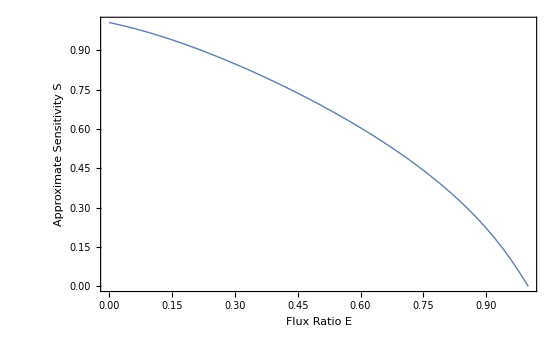

```mathematica
Plot[Abs[SapproxSPtracking[e,50,1,1,100,1]],{e,0,1},LabelStyle->{FontSize->19,FontFamily->"Arial",Black},ImageSize->550,Axes->False,Frame->{True,True,False,False},FrameLabel->{Style["Flux Ratio E",20], Style["Approximate Sensitivity S",20]},PlotRange->All,PlotStyle->Thick]
```

## Derivation of main text equation 9

```mathematica
FxRA = FullSimplify[Xavg*etaxxRA/.Subscript[τ, x]->T/.Subscript[τ, 1]->Tau1/.Subscript[τ, 2]->Tau2/.⟨x⟩->Xavg/.⟨Subscript[z, 1]⟩->Z1avg/.⟨Subscript[z, 2]⟩->Z2avg/.Subscript[β, 1]->b/.Subscript[β, 2]->a*b]
```

(b E1 (-1+E2) (1+a+E1-a E1-E2+E1 (-2+E2) E2)-(-1+E1) (-1+E1 (-1+E2)) (-1+E2) E2 (-1+a (-1+E1)+E2) θ+b E2 (a^2 (-1+E1)^2 (-1+E1 (-1+E2))+(-1+E1 (-1+E2)) (-1+E2)^2-a (-1+E1) (-1+E2) (2+E1+(-2+E1) E1 E2)) T θ+a b^2 (-1+a (-1+E1)+E2) T (E1+E2 (-1+E1 E2)^2 T θ))/((-1+E1 (-1+E2)) E2 (-(-1+E2)^2 (-1+E1-b T)+a^2 b (-1+E1) T (-1+E1+b (-1+E1 E2) T)-a (-1+E2) (E1^2 (1+b T)+(1+b T)^2-E1 (2+b T (3+b E2 T)))) θ)

```mathematica
top=Collect[Simplify[Numerator[FxRA]],b]
```

-(-1+E1) (-1+E1 (-1+E2)) (-1+E2) E2 (-1+a (-1+E1)+E2) θ+a b^2 (-1+a (-1+E1)+E2) T (E1+E2 (-1+E1 E2)^2 T θ)+b (E1 (-1+E2) (1+a+E1-a E1-E2+E1 (-2+E2) E2)+E2 (a^2 (-1+E1)^2 (-1+E1 (-1+E2))+(-1+E1 (-1+E2)) (-1+E2)^2-a (-1+E1) (-1+E2) (2+E1+(-2+E1) E1 E2)) T θ)

```mathematica
bottom=Collect[Denominator[FxRA],b]
```

(-1+E1 (-1+E2)) (-a (-1+E2)+2 a E1 (-1+E2)-a E1^2 (-1+E2)+(-1+E2)^2-E1 (-1+E2)^2) E2 θ+b (-1+E1 (-1+E2)) E2 (-a^2 (-1+E1) T+a^2 (-1+E1) E1 T-2 a (-1+E2) T+3 a E1 (-1+E2) T-a E1^2 (-1+E2) T+(-1+E2)^2 T) θ+b^2 (-1+E1 (-1+E2)) E2 (-a (-1+E2) T^2+a E1 (-1+E2) E2 T^2+a^2 (-1+E1) (-1+E1 E2) T^2) θ

```mathematica
bottomrootsol=Simplify[Solve[bottom==0,b]]
```

{{b→-((1+2 a+a^2-3 a E1-2 a^2 E1+a E1^2+a^2 E1^2-2 E2-2 a E2+3 a E1 E2-a E1^2 E2+E2^2+√(a^4 (-1+E1)^4+(-1+E2)^4+2 a (-1+E1) E1 (-1+E2)^3 (-1+2 E2)+2 a^3 (-1+E1)^3 E1 (1-3 E2+2 E2^2)+a^2 (-1+E1)^2 (-1+E2)^2 (-2+E1^2+E1 (-4+8 E2))))/(2 a (-1+a (-1+E1)+E2) (-1+E1 E2) T))},{b→-((1+2 a+a^2-3 a E1-2 a^2 E1+a E1^2+a^2 E1^2-2 E2-2 a E2+3 a E1 E2-a E1^2 E2+E2^2-√(a^4 (-1+E1)^4+(-1+E2)^4+2 a (-1+E1) E1 (-1+E2)^3 (-1+2 E2)+2 a^3 (-1+E1)^3 E1 (1-3 E2+2 E2^2)+a^2 (-1+E1)^2 (-1+E2)^2 (-2+E1^2+E1 (-4+8 E2))))/(2 a (-1+a (-1+E1)+E2) (-1+E1 E2) T))}}

```mathematica
r1 = b/.bottomrootsol[[1]];
r2= b/.bottomrootsol[[2]];
```

```mathematica
Reduce[r1≥0&&E1>0&&E1<1&&E2>0&&E2<1&&a>0&&T>0]
```

False

```mathematica
Reduce[r2≥ 0&&E1>0&&E1<1&&E2>0&&E2<1&&a>0&&T>0]
```

False

```mathematica
critbvals = Simplify[Solve[D[FxRA,b]==0,b]]
```

{{b→(a^3 (-1+E1)^3 (-1+E2) T (1-E2 T θ+E1 E2^2 T θ)+2 a^2 (-1+E1)^2 (-1+E2)^2 T (1-E2 T θ+E1 E2^2 T θ)+a (-1+E1) (-1+E2)^3 T (1-E2 T θ+E1 E2^2 T θ)-√(a (-1+E1) (-1+E1 (-1+E2)) (-1+E2)^2 (-1+a (-1+E1)+E2)^2 T^2 (a^3 E1^4 E2^3 T^2 θ^2+(1+a-E2)^2 E2 T θ (1-E2+a (-1+E2 T θ))+a E1^3 E2 T θ ((-1+E2)^2 E2+a (-1+E2) (-1+E2+2 E2^2 T θ)-a^2 (-1+E2 T θ+3 E2^2 T θ))-E1 (1+a-E2) (-1+E2^4 T θ (1-a T θ)+E2 (4-3 a^2 T θ)+E2^3 (2-(2+a) T θ+a^2 T^2 θ^2)+E2^2 (-5+(1+a) T θ+a (1+3 a) T^2 θ^2))+E1^2 (-(-1+E2)^4 E2+3 a^3 E2 T θ (-1+E2 T θ+E2^2 T θ)+a (-1+E2)^2 (-1+E2^2 T θ+E2^3 T^2 θ^2+E2 (2-T θ))-a^2 (-1+E2) E2 T θ (-3+4 E2^2 T θ+2 E2 (1+T θ))))))/(a (-1+a (-1+E1)+E2) T^2 (a^2 (-1+E1)^2 (1-E2 T θ+E1 E2^2 T θ)-(-1+E2)^2 (E1^2 (-1+E2) E2+E2 T θ-E1 (-1+2 E2+E2^2 T θ))+a (-1+E1) (-1+E2) (1-2 E2 T θ+E1 (-1+E2+2 E2^2 T θ))))},{b→(a^3 (-1+E1)^3 (-1+E2) T (1-E2 T θ+E1 E2^2 T θ)+2 a^2 (-1+E1)^2 (-1+E2)^2 T (1-E2 T θ+E1 E2^2 T θ)+a (-1+E1) (-1+E2)^3 T (1-E2 T θ+E1 E2^2 T θ)+√(a (-1+E1) (-1+E1 (-1+E2)) (-1+E2)^2 (-1+a (-1+E1)+E2)^2 T^2 (a^3 E1^4 E2^3 T^2 θ^2+(1+a-E2)^2 E2 T θ (1-E2+a (-1+E2 T θ))+a E1^3 E2 T θ ((-1+E2)^2 E2+a (-1+E2) (-1+E2+2 E2^2 T θ)-a^2 (-1+E2 T θ+3 E2^2 T θ))-E1 (1+a-E2) (-1+E2^4 T θ (1-a T θ)+E2 (4-3 a^2 T θ)+E2^3 (2-(2+a) T θ+a^2 T^2 θ^2)+E2^2 (-5+(1+a) T θ+a (1+3 a) T^2 θ^2))+E1^2 (-(-1+E2)^4 E2+3 a^3 E2 T θ (-1+E2 T θ+E2^2 T θ)+a (-1+E2)^2 (-1+E2^2 T θ+E2^3 T^2 θ^2+E2 (2-T θ))-a^2 (-1+E2) E2 T θ (-3+4 E2^2 T θ+2 E2 (1+T θ))))))/(a (-1+a (-1+E1)+E2) T^2 (a^2 (-1+E1)^2 (1-E2 T θ+E1 E2^2 T θ)-(-1+E2)^2 (E1^2 (-1+E2) E2+E2 T θ-E1 (-1+2 E2+E2^2 T θ))+a (-1+E1) (-1+E2) (1-2 E2 T θ+E1 (-1+E2+2 E2^2 T θ))))}}

```mathematica
Reduce[(b/.critbvals[[1]][[1]])>0&&E1≥0&&E1≤1&&E2≥0&&E≤1&&a>0&&T>0&&θ>0]
```

False

```mathematica
canMinb = FxRA/.critbvals[[2]][[1]]; (* first root is strictly negative *)
```

```mathematica
d2Fxdb2 = Simplify[D[D[FxRA,b]]]
```

((-(-1+E2)^2 (-1+E1-b T)+a^2 b (-1+E1) T (-1+E1+b (-1+E1 E2) T)-a (-1+E2) (E1^2 (1+b T)+(1+b T)^2-E1 (2+b T (3+b E2 T)))) (E1 (-1+E2) (1+a+E1-a E1-E2+E1 (-2+E2) E2)+E2 (a^2 (-1+E1)^2 (-1+E1 (-1+E2))+(-1+E1 (-1+E2)) (-1+E2)^2-a (-1+E1) (-1+E2) (2+E1+(-2+E1) E1 E2)) T θ+2 a b (-1+a (-1+E1)+E2) T (E1+E2 (-1+E1 E2)^2 T θ))-T ((-1+E2)^2+a^2 (-1+E1) (-1+E1-2 b T+2 b E1 E2 T)-a (-1+E2) (2+E1^2+2 b T-E1 (3+2 b E2 T))) (b E1 (-1+E2) (1+a+E1-a E1-E2+E1 (-2+E2) E2)-(-1+E1) (-1+E1 (-1+E2)) (-1+E2) E2 (-1+a (-1+E1)+E2) θ+b E2 (a^2 (-1+E1)^2 (-1+E1 (-1+E2))+(-1+E1 (-1+E2)) (-1+E2)^2-a (-1+E1) (-1+E2) (2+E1+(-2+E1) E1 E2)) T θ+a b^2 (-1+a (-1+E1)+E2) T (E1+E2 (-1+E1 E2)^2 T θ)))/((-1+E1 (-1+E2)) E2 ((-1+E2)^2 (-1+E1-b T)-a^2 b (-1+E1) T (-1+E1+b (-1+E1 E2) T)+a (-1+E2) (E1^2 (1+b T)+(1+b T)^2-E1 (2+b T (3+b E2 T))))^2 θ)

```mathematica
Reduce[d2Fxdb2>0&&E1≥0&&E1≤1&&E2≥0&&E≤1&&a>0&&T>0&&θ>0](* thus, the critical point is a maximizer *)
```

False

```mathematica
b0=Simplify[Limit[FxRA,b->0]]
bInfinity=Simplify[Limit[FxRA,b->∞]]
(* Thus, b->∞ must be minimizer in the Subscript[CV, x]<1/√⟨x⟩ regime*)
```

1

(E1+E2 T θ-2 E1 E2^2 T θ+E1^2 E2^3 T θ)/(E2 (1+E1-2 E1 E2+E1^2 (-1+E2) E2) T θ)

```mathematica
Reduce[bInfinity<1&&E1>0&&E1<1&&E2>0&&E2<1&&θ>0&&T>0]
```

0<E2<1&&0<E1<1&&θ>0&&T>-1/(-E2 θ+E1 E2^2 θ)

```mathematica
Reduce[-1/(-E2+E1 E2^2)<1 && E1>0&&E1<1&&E2>0&&E2<1]
(* Thus, Subscript[θτ, x]=Subscript[N, 2]/Subscript[N, x]>1 necessary for noise suppression *)
```

False

```mathematica
critE1vals =Simplify[ Solve[D[bInfinity,E1]==0,E1]]
```

{{E1→(E2^2 T θ-√(E2 (-1+E2+E2 T θ)))/(E2 (-1+E2+E2^2 T θ))},{E1→(E2^2 T θ+√(E2 (-1+E2+E2 T θ)))/(E2 (-1+E2+E2^2 T θ))}}

```mathematica
Reduce[(E1/.critE1vals[[2]][[1]])<1&&E2>0&&E2<1&&a>0&&T>0&&θ>0&&(E1/.critE1vals[[2]][[1]])>0]
```

False

```mathematica
Simplify[1 - (E1/.critE1vals[[1]][[1]])/.E2->1](*this gives S^* as per the Subscript[E, 2]->1 limit of S above *)
```

1/(√(T θ))

```mathematica
canMinE1 =Simplify[bInfinity/.critE1vals[[1]][[1]]] (* second root > 1*)
```

(2 E2^4 T θ (1+T θ)+√(E2 (-1+E2+E2 T θ))-E2 √(E2 (-1+E2+E2 T θ))-3 E2^2 T θ √(E2 (-1+E2+E2 T θ))+2 E2^3 T θ (-1+√(E2 (-1+E2+E2 T θ))))/(E2 T θ (2 E2^3 (1+T θ)+√(E2 (-1+E2+E2 T θ))+E2 (2-3 √(E2 (-1+E2+E2 T θ)))+E2^2 (2+T θ) (-2+√(E2 (-1+E2+E2 T θ)))))

```mathematica
Reduce[E2 (-1+E2+E2 T θ)<0&&T>0&&E1>0&&E1<1&&E2>0&&E2<1&&bInfinity<1&&θ>0]
```

False

```mathematica
d2bInfinitydE12 = Simplify[D[D[bInfinity,E1]]]
```

(1-E2 T θ+2 E1 E2^2 T θ-E1^2 E2 (-1+E2+E2^2 T θ))/(E2 (1+E1-2 E1 E2+E1^2 (-1+E2) E2)^2 T θ)

```mathematica
Reduce[d2bInfinitydE12<0&&E2≥0&&E2≤1&&a>0&&T>0&&θ>0](* thus, the critical point is a minimizer *)
```

False

```mathematica
canMin = FullSimplify[canMinE1/.E2->1]
```

(-1+2 √(T θ))/(T θ)

```mathematica
Reduce[canMinE1 <canMin&&T==1&&E1>0&&E1<1&&E2>0&&E2<1&&bInfinity<1&&θ>0]
```

False

## Derivation of main text equations 12 and 13

```mathematica
MmatrISA = Mmatr/.E1->1/.E2->1/.Subscript[h, x]->0/.Subscript[h, 1]->0;
MatrixForm[MmatrISA]
```

(1/τ_x | 0 | -h_2/τ_x
0 | 1/τ_1 | 1/τ_1
-1/τ_2 | 1/τ_2 | 1/τ_2)

```mathematica
DmatrISA = Dmatr/.E1->1/.E2->1;
MatrixForm[DmatrISA]
```

(2/(⟨x⟩ τ_x) | 0 | 0
0 | 2/(⟨z_1⟩ τ_1) | 1/2 (1/(⟨z_2⟩ τ_1)+1/(⟨z_1⟩ τ_2))
0 | 1/2 (1/(⟨z_2⟩ τ_1)+1/(⟨z_1⟩ τ_2)) | 2/(⟨z_2⟩ τ_2))

```mathematica
covsISA=Solve[MmatrISA.ETAmatr+Transpose[MmatrISA.ETAmatr]==DmatrISA,Flatten[ETAmatr]][[1]];
```

```mathematica
etaxxISA= Collect[(Subscript[η, xx]/.covsISA), {1/⟨x⟩,1/⟨Subscript[z, 1]⟩,1/⟨Subscript[z, 2]⟩}]
```

(-h_2 τ_1^2 τ_2-h_2 τ_1^2 τ_x-h_2 τ_1 τ_2 τ_x)/(2 ⟨z_1⟩ (τ_1^2 τ_2-h_2 τ_1^2 τ_2+τ_1 τ_2^2+τ_1^2 τ_x-h_2 τ_1^2 τ_x+2 τ_1 τ_2 τ_x+τ_2^2 τ_x))+(2 τ_1^2 τ_2-2 h_2 τ_1^2 τ_2+2 τ_1 τ_2^2+2 τ_1^2 τ_x+4 τ_1 τ_2 τ_x+2 τ_2^2 τ_x)/(2 ⟨x⟩ (τ_1^2 τ_2-h_2 τ_1^2 τ_2+τ_1 τ_2^2+τ_1^2 τ_x-h_2 τ_1^2 τ_x+2 τ_1 τ_2 τ_x+τ_2^2 τ_x))+(2 h_2^2 τ_1^2 τ_2-h_2 τ_1 τ_2^2-h_2 τ_1 τ_2 τ_x-h_2 τ_2^2 τ_x)/(2 ⟨z_2⟩ (τ_1^2 τ_2-h_2 τ_1^2 τ_2+τ_1 τ_2^2+τ_1^2 τ_x-h_2 τ_1^2 τ_x+2 τ_1 τ_2 τ_x+τ_2^2 τ_x))

```mathematica
lim = Simplify[Limit[(etaxxISA/.Subscript[τ, 1]->⟨Subscript[z, 1]⟩/(θ*⟨x⟩)/.Subscript[τ, 2]->⟨Subscript[z, 2]⟩/(θ*⟨x⟩)),{⟨Subscript[z, 1]⟩->∞,⟨Subscript[z, 2]⟩->0}]]
```

(h_2^2+θ τ_x)/(θ ⟨x⟩ τ_x-θ ⟨x⟩ h_2 τ_x)

```mathematica
Reduce[etaxxISA < lim && ⟨x⟩>0 && ⟨Subscript[z, 1]⟩>0&&⟨Subscript[z, 2]⟩>0&&Subscript[τ, x]>0&&Subscript[τ, 1]==⟨Subscript[z, 1]⟩/(θ*⟨x⟩)&&Subscript[τ, 2]==⟨Subscript[z, 2]⟩/(θ*⟨x⟩)&&θ>0&&etaxxISA>0&&etaxxISA<1/⟨x⟩&&Subscript[h, 2]<0]
```

False

```mathematica
Solve[D[lim,Subscript[h, 2]]==0,Subscript[h, 2]]
```

{{h_2→1-√(1+θ τ_x)},{h_2→1+√(1+θ τ_x)}}

```mathematica
criticalh2 = Subscript[h, 2]/.%[[1]]
```

1-√(1+θ τ_x)

```mathematica
canboundISA =Simplify[ lim/.Subscript[h, 2]->criticalh2]
```

(2+2 θ τ_x-2 √(1+θ τ_x))/(θ ⟨x⟩ τ_x √(1+θ τ_x))

```mathematica
Reduce[(2+2 θ Subscript[τ, x]-2 √(1+θ Subscript[τ, x]))/(θ ⟨x⟩ Subscript[τ, x] √(1+θ Subscript[τ, x]))==2/(⟨x⟩*(1+√(1+θ Subscript[τ, x])))]
```

True

```mathematica
Reduce[lim < canboundISA && ⟨x⟩>0 && ⟨Subscript[z, 1]⟩>0&&⟨Subscript[z, 2]⟩>0&&Subscript[τ, x]>0&&Subscript[τ, 1]==⟨Subscript[z, 1]⟩/(θ*⟨x⟩)&&Subscript[τ, 2]==⟨Subscript[z, 2]⟩/(θ*⟨x⟩)&&θ>0&&canboundISA>0&&canboundISA<1/⟨x⟩&&Subscript[h, 2]<0]
```

False

## Linear noise analysis of a minimal antithetic integral rein control system

### Comparison with minimal idealized sensor-actuated system

```mathematica
MmatrAIRC = Mmatr/.E1->1/.E2->1/.Subscript[h, x]->0;
MatrixForm[MmatrISA]
```

(1/τ_x | 0 | -h_2/τ_x
0 | 1/τ_1 | 1/τ_1
-1/τ_2 | 1/τ_2 | 1/τ_2)

```mathematica
DmatrAIRC = Dmatr/.E1->1/.E2->1/.Subscript[h, x]->0;
MatrixForm[DmatrAIRC]
```

(2/(⟨x⟩ τ_x) | 0 | 0
0 | 2/(⟨z_1⟩ τ_1) | 1/2 (1/(⟨z_2⟩ τ_1)+1/(⟨z_1⟩ τ_2))
0 | 1/2 (1/(⟨z_2⟩ τ_1)+1/(⟨z_1⟩ τ_2)) | 2/(⟨z_2⟩ τ_2))

```mathematica
covsAIRC=Solve[MmatrAIRC.ETAmatr+Transpose[MmatrAIRC.ETAmatr]==DmatrAIRC,Flatten[ETAmatr]][[1]];
```

```mathematica
etaxxAIRC= Collect[(Subscript[η, xx]/.covsAIRC), {1/⟨x⟩,1/⟨Subscript[z, 1]⟩,1/⟨Subscript[z, 2]⟩}]
```

-(h_1 τ_1^2 τ_2-h_2 τ_1^2 τ_2+h_1 h_2 τ_1^2 τ_2+2 h_1^2 τ_1 τ_2^2+h_1 τ_1^2 τ_x-h_2 τ_1^2 τ_x+h_1 τ_1 τ_2 τ_x-h_2 τ_1 τ_2 τ_x)/(2 ⟨z_1⟩ (-τ_1^2 τ_2+h_2 τ_1^2 τ_2-τ_1 τ_2^2-τ_1^2 τ_x+h_2 τ_1^2 τ_x-2 τ_1 τ_2 τ_x+h_1 τ_1 τ_2 τ_x-τ_2^2 τ_x))-(2 τ_1^2 τ_2-2 h_2 τ_1^2 τ_2+2 τ_1 τ_2^2+2 τ_1^2 τ_x+4 τ_1 τ_2 τ_x+2 τ_2^2 τ_x)/(2 ⟨x⟩ (-τ_1^2 τ_2+h_2 τ_1^2 τ_2-τ_1 τ_2^2-τ_1^2 τ_x+h_2 τ_1^2 τ_x-2 τ_1 τ_2 τ_x+h_1 τ_1 τ_2 τ_x-τ_2^2 τ_x))-(2 h_2^2 τ_1^2 τ_2+h_1 τ_1 τ_2^2-h_2 τ_1 τ_2^2+h_1 h_2 τ_1 τ_2^2+h_1 τ_1 τ_2 τ_x-h_2 τ_1 τ_2 τ_x+h_1 τ_2^2 τ_x-h_2 τ_2^2 τ_x)/(2 ⟨z_2⟩ (-τ_1^2 τ_2+h_2 τ_1^2 τ_2-τ_1 τ_2^2-τ_1^2 τ_x+h_2 τ_1^2 τ_x-2 τ_1 τ_2 τ_x+h_1 τ_1 τ_2 τ_x-τ_2^2 τ_x))

```mathematica
lim = Simplify[Limit[(etaxxAIRC/.Subscript[τ, 1]->⟨Subscript[z, 1]⟩/(θ*⟨x⟩)/.Subscript[τ, 2]->⟨Subscript[z, 2]⟩/(θ*⟨x⟩)),{⟨Subscript[z, 1]⟩->∞,⟨Subscript[z, 2]⟩->0}]]
```

(h_2^2+θ τ_x)/(θ ⟨x⟩ τ_x-θ ⟨x⟩ h_2 τ_x)

```mathematica
Reduce[etaxxAIRC < etaxxISA && ⟨x⟩>0 && ⟨Subscript[z, 1]⟩>0&&⟨Subscript[z, 2]⟩>0&&Subscript[τ, x]>0&&Subscript[τ, 1]==⟨Subscript[z, 1]⟩/(θ*⟨x⟩)&&Subscript[τ, 2]==⟨Subscript[z, 2]⟩/(θ*⟨x⟩)&&θ>0&&etaxxAIRC>0&&etaxxAIRC<1/⟨x⟩&&Subscript[h, 2]<0&&Subscript[h, 1]>0]
```

False

### Comparison of data from Gupta 2019 with open-loop fluctuations

#### Exact solution to linear constitutive gene expression model

```mathematica
MmatrOL = {1/Subscript[τ, r]*{1, 0},1/Subscript[τ, p]*{-1, 1}};
MatrixForm[MmatrOL]
```

(1/τ_r | 0
-1/τ_p | 1/τ_p)

```mathematica
DmatrOL = {{2/(⟨r⟩ Subscript[τ, r]), 0},{0, 2/(⟨p⟩ Subscript[τ, p])}};
MatrixForm[DmatrOL]
```

(2/(⟨r⟩ τ_r) | 0
0 | 2/(⟨p⟩ τ_p))

```mathematica
ETAmatrOL={{Subscript[η, rr],Subscript[η, rp]},{Subscript[η, rp],Subscript[η, pp]}};
MatrixForm[ETAmatrOL]
```

(η_rr | η_rp
η_rp | η_pp)

```mathematica
covsOL=Solve[MmatrOL.ETAmatrOL+Transpose[MmatrOL.ETAmatrOL]==DmatrOL,Flatten[ETAmatrOL]][[1]];
```

```mathematica
etappOL= Collect[Simplify[(Subscript[η, pp]/.covsOL)], {1/⟨r⟩,1/⟨p⟩}]
```

1/⟨p⟩+τ_r/(⟨r⟩ (τ_p+τ_r))

#### Solve flux balance equations such that ⟨p⟩=μ/θ

```mathematica
AvgSol=Solve[Subscript[γ, p]*⟨p⟩ == Subscript[k, p]*⟨r⟩&&⟨p⟩==μ/θ, {⟨r⟩,⟨p⟩}]
```

{{⟨r⟩→(μ γ_p)/(θ k_p),⟨p⟩→μ/θ}}

#### Evaluate open-loop variance for each parameter set reported in Gupta 2019

```mathematica
VARppOL = Simplify[etappOL*⟨p⟩^2/.AvgSol[[1]]/.Subscript[τ, r]->1/Subscript[γ, r]/.Subscript[τ, p]->1/Subscript[γ, p]]
```

(μ (k_p+γ_p+γ_r))/(θ (γ_p+γ_r))

```mathematica
VARppOL/.μ-> 100/.θ->5/.Subscript[k, p]-> 5/.Subscript[γ, r]->5/.Subscript[γ, p]->5
```

30

```mathematica
VARppOL/.μ-> 100/.θ->5/.Subscript[k, p]-> 5/.Subscript[γ, r]->5/.Subscript[γ, p]->0.1
```

39.6078

## Linear noise analysis of idealized reference-actuated antithetic integral feedback system with nonlinear actuation

```mathematica
MmatrIRANL = Mmatr/.E1->1/.E2->1/.Subscript[h, x]->0/.Subscript[h, 2]->0;
MatrixForm[MmatrIRANL]
```

(1/τ_x | -h_1/τ_x | 0
0 | 1/τ_1 | 1/τ_1
-1/τ_2 | 1/τ_2 | 1/τ_2)

```mathematica
DmatrIRANL = Dmatr/.E1->1/.E2->1;
MatrixForm[DmatrIRANL]
```

(2/(⟨x⟩ τ_x) | 0 | 0
0 | 2/(⟨z_1⟩ τ_1) | 1/2 (1/(⟨z_2⟩ τ_1)+1/(⟨z_1⟩ τ_2))
0 | 1/2 (1/(⟨z_2⟩ τ_1)+1/(⟨z_1⟩ τ_2)) | 2/(⟨z_2⟩ τ_2))

```mathematica
covsIRANL=Solve[MmatrIRANL.ETAmatr+Transpose[MmatrIRANL.ETAmatr]==DmatrIRANL,Flatten[ETAmatr]][[1]];
```

```mathematica
etaxxIRANL= Collect[(Subscript[η, xx]/.covsIRANL), {1/⟨x⟩,1/⟨Subscript[z, 1]⟩,1/⟨Subscript[z, 2]⟩}]
```

-(-h_1 τ_1^2 τ_2-2 h_1^2 τ_1 τ_2^2-h_1 τ_1^2 τ_x-h_1 τ_1 τ_2 τ_x)/(2 ⟨z_1⟩ (τ_1^2 τ_2+τ_1 τ_2^2+τ_1^2 τ_x+2 τ_1 τ_2 τ_x-h_1 τ_1 τ_2 τ_x+τ_2^2 τ_x))-(-2 τ_1^2 τ_2-2 τ_1 τ_2^2-2 τ_1^2 τ_x-4 τ_1 τ_2 τ_x-2 τ_2^2 τ_x)/(2 ⟨x⟩ (τ_1^2 τ_2+τ_1 τ_2^2+τ_1^2 τ_x+2 τ_1 τ_2 τ_x-h_1 τ_1 τ_2 τ_x+τ_2^2 τ_x))-(-h_1 τ_1 τ_2^2-h_1 τ_1 τ_2 τ_x-h_1 τ_2^2 τ_x)/(2 ⟨z_2⟩ (τ_1^2 τ_2+τ_1 τ_2^2+τ_1^2 τ_x+2 τ_1 τ_2 τ_x-h_1 τ_1 τ_2 τ_x+τ_2^2 τ_x))

```mathematica
Reduce[etaxxIRANL < 1/⟨x⟩ && ⟨x⟩>0 && ⟨Subscript[z, 1]⟩>0&&⟨Subscript[z, 2]⟩>0&&Subscript[τ, x]>0&&Subscript[τ, 1]==⟨Subscript[z, 1]⟩/μ&&Subscript[τ, 2]==⟨Subscript[z, 2]⟩/μ&&μ>0&&etaxxIRANL>0&&Subscript[h, 1]>0]
```

False

```mathematica
canboundIRANL = Simplify[Limit[(etaxxIRANL/.Subscript[τ, 2]->⟨Subscript[z, 2]⟩/μ),⟨Subscript[z, 2]⟩->∞]]
```

1/⟨x⟩+(h_1^2 τ_1)/(⟨z_1⟩ (τ_1+τ_x))

## Derivation of approximate sensitivity coefficient for the sensor-actuated system with control species dilution

### Linear noise approximation

```mathematica
MmatrSA = Mmatr/.Subscript[h, 1]->0/.Subscript[h, x]->0;
MatrixForm[MmatrSA]
```

(1/τ_x | 0 | -h_2/τ_x
0 | 1/τ_1 | E1/τ_1
-1/τ_2 | E2/τ_2 | 1/τ_2)

```mathematica
DmatrSA = Dmatr;
MatrixForm[DmatrSA]
```

(2/(⟨x⟩ τ_x) | 0 | 0
0 | 2/(⟨z_1⟩ τ_1) | 1/2 (E1/(⟨z_2⟩ τ_1)+E2/(⟨z_1⟩ τ_2))
0 | 1/2 (E1/(⟨z_2⟩ τ_1)+E2/(⟨z_1⟩ τ_2)) | 2/(⟨z_2⟩ τ_2))

```mathematica
covsSA=Solve[MmatrSA.ETAmatr+Transpose[MmatrSA.ETAmatr]==DmatrSA,Flatten[ETAmatr]][[1]];
```

```mathematica
etaxxSA= Collect[(Subscript[η, xx]/.covsSA), {1/⟨x⟩,1/⟨Subscript[z, 1]⟩,1/⟨Subscript[z, 2]⟩}]
```

-(-E2^2 h_2^2 τ_1^2 τ_2-E2^2 h_2^2 τ_1^2 τ_x-E2^2 h_2^2 τ_1 τ_2 τ_x)/(2 ⟨z_1⟩ (-1+E1 E2+h_2) (-τ_1^2 τ_2+h_2 τ_1^2 τ_2-τ_1 τ_2^2-τ_1^2 τ_x+h_2 τ_1^2 τ_x-2 τ_1 τ_2 τ_x-τ_2^2 τ_x-τ_1 τ_x^2+E1 E2 τ_1 τ_x^2-τ_2 τ_x^2+E1 E2 τ_2 τ_x^2))-(-2 h_2^2 τ_1^2 τ_2+2 E1 E2 h_2^2 τ_1^2 τ_2+2 h_2^3 τ_1^2 τ_2-2 h_2^2 τ_1 τ_2^2+E1 E2 h_2^2 τ_1 τ_2^2-2 h_2^2 τ_1 τ_2 τ_x+E1 E2 h_2^2 τ_1 τ_2 τ_x-2 h_2^2 τ_2^2 τ_x+E1 E2 h_2^2 τ_2^2 τ_x)/(2 ⟨z_2⟩ (-1+E1 E2+h_2) (-τ_1^2 τ_2+h_2 τ_1^2 τ_2-τ_1 τ_2^2-τ_1^2 τ_x+h_2 τ_1^2 τ_x-2 τ_1 τ_2 τ_x-τ_2^2 τ_x-τ_1 τ_x^2+E1 E2 τ_1 τ_x^2-τ_2 τ_x^2+E1 E2 τ_2 τ_x^2))-(-2 τ_1^2 τ_2+2 E1 E2 τ_1^2 τ_2+4 h_2 τ_1^2 τ_2-2 E1 E2 h_2 τ_1^2 τ_2-2 h_2^2 τ_1^2 τ_2-2 τ_1 τ_2^2+2 E1 E2 τ_1 τ_2^2+2 h_2 τ_1 τ_2^2-2 τ_1^2 τ_x+2 E1 E2 τ_1^2 τ_x+2 h_2 τ_1^2 τ_x-4 τ_1 τ_2 τ_x+4 E1 E2 τ_1 τ_2 τ_x+2 h_2 τ_1 τ_2 τ_x+2 E1 E2 h_2 τ_1 τ_2 τ_x-2 τ_2^2 τ_x+2 E1 E2 τ_2^2 τ_x+2 h_2 τ_2^2 τ_x-2 τ_1 τ_x^2+4 E1 E2 τ_1 τ_x^2-2 E1^2 E2^2 τ_1 τ_x^2-2 τ_2 τ_x^2+4 E1 E2 τ_2 τ_x^2-2 E1^2 E2^2 τ_2 τ_x^2)/(2 ⟨x⟩ (-1+E1 E2+h_2) (-τ_1^2 τ_2+h_2 τ_1^2 τ_2-τ_1 τ_2^2-τ_1^2 τ_x+h_2 τ_1^2 τ_x-2 τ_1 τ_2 τ_x-τ_2^2 τ_x-τ_1 τ_x^2+E1 E2 τ_1 τ_x^2-τ_2 τ_x^2+E1 E2 τ_2 τ_x^2))

```mathematica
eta12SA= Collect[(Subscript[η, 12]/.covsSA), {1/⟨x⟩,1/⟨Subscript[z, 1]⟩,1/⟨Subscript[z, 2]⟩}]
```

-(E2 τ_1^2 τ_2-E2 h_2 τ_1^2 τ_2+E2 τ_1^2 τ_x-E2 h_2 τ_1^2 τ_x+E2 τ_1 τ_2 τ_x-E2 h_2 τ_1 τ_2 τ_x+E2 τ_1 τ_x^2-E1 E2^2 τ_1 τ_x^2-E2 h_2 τ_1 τ_x^2)/(2 ⟨z_1⟩ (-1+E1 E2+h_2) (-τ_1^2 τ_2+h_2 τ_1^2 τ_2-τ_1 τ_2^2-τ_1^2 τ_x+h_2 τ_1^2 τ_x-2 τ_1 τ_2 τ_x-τ_2^2 τ_x-τ_1 τ_x^2+E1 E2 τ_1 τ_x^2-τ_2 τ_x^2+E1 E2 τ_2 τ_x^2))-(2 E1 τ_1 τ_2 τ_x+2 E1 τ_1 τ_x^2+2 E1 τ_2 τ_x^2)/(2 ⟨x⟩ (-1+E1 E2+h_2) (-τ_1^2 τ_2+h_2 τ_1^2 τ_2-τ_1 τ_2^2-τ_1^2 τ_x+h_2 τ_1^2 τ_x-2 τ_1 τ_2 τ_x-τ_2^2 τ_x-τ_1 τ_x^2+E1 E2 τ_1 τ_x^2-τ_2 τ_x^2+E1 E2 τ_2 τ_x^2))-(E1 τ_1 τ_2^2+E1 h_2 τ_1 τ_2^2+E1 τ_1 τ_2 τ_x+E1 h_2 τ_1 τ_2 τ_x+E1 τ_2^2 τ_x+E1 h_2 τ_2^2 τ_x+E1 τ_2 τ_x^2-E1^2 E2 τ_2 τ_x^2-E1 h_2 τ_2 τ_x^2)/(2 ⟨z_2⟩ (-1+E1 E2+h_2) (-τ_1^2 τ_2+h_2 τ_1^2 τ_2-τ_1 τ_2^2-τ_1^2 τ_x+h_2 τ_1^2 τ_x-2 τ_1 τ_2 τ_x-τ_2^2 τ_x-τ_1 τ_x^2+E1 E2 τ_1 τ_x^2-τ_2 τ_x^2+E1 E2 τ_2 τ_x^2))

### Self-consistent expressions for averages and lifetimes in terms the flux ratio parameters E_1 and E_2

```mathematica
Xavg =μ/θ*E1/E2;
Z1avg = μ/Subscript[β, 1]*(1-E1);
Z2avg = μ/Subscript[β, 2]*E1/E2*(1-E2);
Z1Z2avg = μ/γ*E1;
Tau1 = (1-E1)/Subscript[β, 1];
Tau2 = (1-E2)/Subscript[β, 2];
```

```mathematica
Reduce[μ==γ*Z1Z2avg + Subscript[β, 1]*Z1avg&&θ*Xavg==γ*Z1Z2avg + Subscript[β, 2]*Z2avg && Tau1 == Z1avg/μ&&Tau2== Z2avg/(θ*Xavg)&&E1 ==(γ*Z1Z2avg)/μ&&E2 ==(γ*Z1Z2avg)/(θ*Xavg)]
```

True

### Make substitutions and solve for the approximate sensitivity coefficient

```mathematica
eta12identity[bx_] = Simplify[Z1Z2avg/(Z1avg*Z2avg)-1]/.E1->E1[bx]/.E2->E2[bx] (* let bx be a stand-in for Subscript[β, x] *)
```

-1+(E2[T] β_1 β_2)/(γ μ (-1+E1[T]) (-1+E2[T]))

```mathematica
eta12LNA[bx_] = Simplify[eta12SA/.Subscript[τ, x]->(1/bx)/.Subscript[τ, 1]->Tau1/.Subscript[τ, 2]->Tau2/.⟨x⟩->Xavg/.⟨Subscript[z, 1]⟩->Z1avg/.⟨Subscript[z, 2]⟩->Z2avg/.E1->E1[bx]/.E2->E2[bx]]/.Subscript[h, 2]->h[bx]
```

-((E2[bx] β_1 β_2 (-bx^2-bx θ-bx β_1-θ β_1+(bx+θ) E2[bx] (bx+β_1)-bx β_2-θ β_2-β_1 β_2+h[bx] β_1 β_2+E1[bx] ((bx+θ) (bx+β_2)+E2[bx] (-bx (bx+θ)+β_1 β_2))))/(μ (-1+E1[bx] E2[bx]+h[bx]) (bx (-1+E1[bx])^2 (-1+h[bx]) (-bx+bx E2[bx]-β_2) β_2+(-1+E2[bx]) β_1^2 (-bx-β_2+E2[bx] (bx+E1[bx] β_2))-(-1+E1[bx]) β_1 (bx^2 E2[bx]^2+(bx+β_2)^2-E2[bx] (2 bx^2+2 bx β_2+E1[bx] β_2^2)))))

```mathematica
X[bx_] = Xavg/.E1->E1[bx]/.E2->E2[bx];
Z2[bx_] = Z2avg/.E1->E1[bx]/.E2->E2[bx];
```

```mathematica
dE12dTapprox = Solve[Subscript[h, 2]*(bx*X[bx])/Z2[bx]*D[Z2[bx],bx] == D[bx*X[bx],bx]&&D[eta12LNA[bx], bx]==D[eta12identity[bx] ,bx],{E1'[bx],E2'[bx]}]
```

{{E1'[bx]→-((μ E1[bx] (-(β_1 β_2)/1+14))/(θ E2[bx])+((bx μ E1[bx])/(θ (E212])^2)-1-(bx μ 1 h_2)/(θ 1 1)) 1)/(((bx μ E1[bx])/(θ E2[bx]^2)-(bx μ E1[bx] h_2)/(θ E2[bx]^2)-(bx μ E1[bx] h_2)/(θ (1-E2[bx]) E2[bx])) (1)-(-(bx μ)/(θ 1)+1/(θ 1)) (1)),E2'[bx]→1/1+1}}
 |  |  |  |

```mathematica
SapproxSA[E1_,E2_,μ_,θ_,b1_,b2_,γ_,h_, q_,bx_] = bx/X[bx]*D[X[bx],bx]/.E1'[bx]->(E1'[bx]/.dE12dTapprox[[1]])/.E2'[bx]->(E2'[bx]/.dE12dTapprox[[1]])/.E1[bx]->E1/.E2[bx]->E2/.Subscript[β, 1]->b1/.Subscript[β, 2]->b2/.h[bx]->h/.h'[bx]->q
```

(bx E2 θ (-(μ ((E1 (1) μ)/(E2 θ)+(1) 1))/(E2 θ (-(1) (-1+1)+1))-1/(E2^2 θ)))/(E1 μ)
 |  |  |  |

```mathematica
Limit[SapproxSA[E1,E2,μ,θ,b1,b2,γ,h,q,bx],E2->1](* in absolute value --> (1-Subscript[E, 1])/(1 - Subscript[E, 1] - Subscript[h, 2]), since Subscript[E, 1]≤1 and Subscript[h, 2]<0*)
```

(1-E1)/(-1+E1+h_2)

## Analogue of main text equation 10 for sensor-actuated system with dilution

```mathematica
FxSA = FullSimplify[Xavg*etaxxSA/.Subscript[τ, x]->T/.Subscript[τ, 1]->Tau1/.Subscript[τ, 2]->Tau2/.⟨x⟩->Xavg/.⟨Subscript[z, 1]⟩->Z1avg/.⟨Subscript[z, 2]⟩->Z2avg/.Subscript[β, 1]->b/.Subscript[β, 2]->a*b]
```

-(((-1+a (-1+E1)+E2) (-1+E1 E2) (-1+E1+E2-E1 E2+b (-1+a (-1+E1)+E2) T+a b^2 (-1+E1 E2) T^2) θ+h_2 ((a^2 b (-1+E1)^2 T-(-1+E2)^2 (-1+E1-b T)+a (-1+E1) (-1+E2) (2+b T+E1 (-2+E2 (-1+E1+b T)))) θ+a h_2 (b (-1+E1) (1-E2+a (-1+E1) (-1+E1 E2))+b^2 (-1+a (-1+E1)+E2) T+(-1+E1)^2 (-1+E2) θ+a b (-1+E1)^2 h_2)))/(θ (-1+E1 E2+h_2) (-(-1+a (-1+E1)+E2) (-1+E1+E2-E1 E2+b (-1+a (-1+E1)+E2) T+a b^2 (-1+E1 E2) T^2)+a (-1+E1)^2 (1-E2+a b T) h_2)))

```mathematica
top=Collect[Simplify[Numerator[FxSA]],b]
```

-(1-a (-1+E1)-E2) (-1+E1 E2) θ+E1 (1-a (-1+E1)-E2) (-1+E1 E2) θ+(1-a (-1+E1)-E2) E2 (-1+E1 E2) θ-E1 (1-a (-1+E1)-E2) E2 (-1+E1 E2) θ-2 a (-1+E1) (-1+E2) θ h_2+2 a (-1+E1) E1 (-1+E2) θ h_2-(-1+E2)^2 θ h_2+E1 (-1+E2)^2 θ h_2+a (-1+E1) E1 (-1+E2) E2 θ h_2-a (-1+E1) E1^2 (-1+E2) E2 θ h_2-a (-1+E1)^2 (-1+E2) θ h_2^2+b^2 (a (1-a (-1+E1)-E2) (-1+E1 E2)^2 T^2 θ-a (-1+a (-1+E1)+E2) T h_2^2)+b ((1-a (-1+E1)-E2) (-1+a (-1+E1)+E2) (-1+E1 E2) T θ-a^2 (-1+E1)^2 T θ h_2-a (-1+E1) (-1+E2) T θ h_2-(-1+E2)^2 T θ h_2-a (-1+E1) E1 (-1+E2) E2 T θ h_2-a (-1+E1) (1-E2+a (-1+E1) (-1+E1 E2)) h_2^2-a^2 (-1+E1)^2 h_2^3)

```mathematica
bottom=Collect[Denominator[FxSA],b]
```

a b^2 (1-a (-1+E1)-E2) (-1+E1 E2) T^2 θ (-1+E1 E2+h_2)+θ (-1+E1 E2+h_2) (-1+a (-1+E1)+E1 (1-a (-1+E1)-E2)+E2+(1-a (-1+E1)-E2) E2-E1 (1-a (-1+E1)-E2) E2+a (-1+E1)^2 h_2-a (-1+E1)^2 E2 h_2)+b θ (-1+E1 E2+h_2) ((1-a (-1+E1)-E2) (-1+a (-1+E1)+E2) T+a^2 (-1+E1)^2 T h_2)

```mathematica
bottomrootsol=Simplify[Solve[bottom==0,b]]
```

{{b→(-1-2 a-a^2+2 a E1+2 a^2 E1-a^2 E1^2+2 E2+2 a E2-2 a E1 E2-E2^2+a^2 h_2-2 a^2 E1 h_2+a^2 E1^2 h_2+√((-1+a (-1+E1)+E2)^2 (a^2 (-1+E1)^2+(-1+E2)^2+2 a (-1+E1) (-1+E2) (-1+2 E1 E2))-2 a^2 (-1+E1)^2 (a^2 (-1+E1)^2+2 a (-1+E1) E1 (-1+E2) E2+(-1+E2)^2 (-1+2 E1 E2)) h_2+a^4 (-1+E1)^4 h_2^2))/(2 a (-1+a (-1+E1)+E2) (-1+E1 E2) T)},{b→-((1+2 a+a^2-2 a E1-2 a^2 E1+a^2 E1^2-2 E2-2 a E2+2 a E1 E2+E2^2-a^2 h_2+2 a^2 E1 h_2-a^2 E1^2 h_2+√((-1+a (-1+E1)+E2)^2 (a^2 (-1+E1)^2+(-1+E2)^2+2 a (-1+E1) (-1+E2) (-1+2 E1 E2))-2 a^2 (-1+E1)^2 (a^2 (-1+E1)^2+2 a (-1+E1) E1 (-1+E2) E2+(-1+E2)^2 (-1+2 E1 E2)) h_2+a^4 (-1+E1)^4 h_2^2))/(2 a (-1+a (-1+E1)+E2) (-1+E1 E2) T))}}

```mathematica
r1 = b/.bottomrootsol[[1]];
r2= b/.bottomrootsol[[2]];
```

```mathematica
Reduce[r1≥0&&E1≥0&&E1≤1&&E2≥0&&E≤1&&a>0&&T>0]
```

False

```mathematica
Reduce[r2≥ 0&&E1≥0&&E1≤1&&E2≥0&&E≤1&&a>0&&T>0]
```

False

```mathematica
critbvals = Simplify[Solve[D[FxSA,b]==0,b]]
```

{{b→(-T^2 θ-2 a T^2 θ-a^2 T^2 θ+E1 T^2 θ+4 a E1 T^2 θ+3 a^2 E1 T^2 θ-2 a E1^2 T^2 θ-3 a^2 E1^2 T^2 θ+a^2 E1^3 T^2 θ+3 E2 T^2 θ+4 a E2 T^2 θ+a^2 E2 T^2 θ-2 E1 E2 T^2 θ-6 a E1 E2 T^2 θ-2 a^2 E1 E2 T^2 θ-E1^2 E2 T^2 θ+2 a E1^3 E2 T^2 θ+2 a^2 E1^3 E2 T^2 θ-a^2 E1^4 E2 T^2 θ-3 E2^2 T^2 θ-2 a E2^2 T^2 θ-a^2 E1 E2^2 T^2 θ+3 E1^2 E2^2 T^2 θ+6 a E1^2 E2^2 T^2 θ+3 a^2 E1^2 E2^2 T^2 θ-4 a E1^3 E2^2 T^2 θ-3 a^2 E1^3 E2^2 T^2 θ+a^2 E1^4 E2^2 T^2 θ+E2^3 T^2 θ+2 E1 E2^3 T^2 θ+2 a E1 E2^3 T^2 θ-3 E1^2 E2^3 T^2 θ-4 a E1^2 E2^3 T^2 θ+2 a E1^3 E2^3 T^2 θ-E1 E2^4 T^2 θ+E1^2 E2^4 T^2 θ-(-1+E1) (-1+E2) (-1+a (-1+E1)+E2) T (-1+E2+a (-1+E1) (1+(-1+E1 E2) T θ)) h_2+a (-1+E1)^2 (-1+E2) (-1+a (-1+E1)+E2) T h_2^2+√(a (-1+E1)^3 E1 (-1+E2) E2 (-1+a (-1+E1)+E2) T^2 (-1+E1 E2+h_2) (1+a-a E1-E2+a (-1+E1) h_2) ((-1+a (-1+E1)+E2)^2 (-1+E1 E2) T^2 θ^2+(-(-1+E2)^2+2 a (-1+E1) (-1+E2) (-2+E1 E2)+a^2 (-1+E1)^2 (-3+2 E1 E2)) T θ h_2+a (-1+E1) (2-2 E2+a (-1+E1) (-2+E1 E2+T θ)) h_2^2+a^2 (-1+E1)^2 h_2^3)))/((-1+a (-1+E1)+E2) T^2 ((-1+E1 E2) ((-1+E2)^2+a^2 (-1+E1)^2 E1 E2+a (-1+E1) (-1+E2) (1+E1 E2)) T θ+(-(-1+E2)^2+a^2 (-1+E1)^2 E1 E2 (-2+E1 E2)-a (-1+E1) (-1+E2) (1+E1 E2)) h_2+a^2 (-1+E1)^2 E1 E2 h_2^2))},{b→-((T^2 θ+2 a T^2 θ+a^2 T^2 θ-E1 T^2 θ-4 a E1 T^2 θ-3 a^2 E1 T^2 θ+2 a E1^2 T^2 θ+3 a^2 E1^2 T^2 θ-a^2 E1^3 T^2 θ-3 E2 T^2 θ-4 a E2 T^2 θ-a^2 E2 T^2 θ+2 E1 E2 T^2 θ+6 a E1 E2 T^2 θ+2 a^2 E1 E2 T^2 θ+E1^2 E2 T^2 θ-2 a E1^3 E2 T^2 θ-2 a^2 E1^3 E2 T^2 θ+a^2 E1^4 E2 T^2 θ+3 E2^2 T^2 θ+2 a E2^2 T^2 θ+a^2 E1 E2^2 T^2 θ-3 E1^2 E2^2 T^2 θ-6 a E1^2 E2^2 T^2 θ-3 a^2 E1^2 E2^2 T^2 θ+4 a E1^3 E2^2 T^2 θ+3 a^2 E1^3 E2^2 T^2 θ-a^2 E1^4 E2^2 T^2 θ-E2^3 T^2 θ-2 E1 E2^3 T^2 θ-2 a E1 E2^3 T^2 θ+3 E1^2 E2^3 T^2 θ+4 a E1^2 E2^3 T^2 θ-2 a E1^3 E2^3 T^2 θ+E1 E2^4 T^2 θ-E1^2 E2^4 T^2 θ+(-1+E1) (-1+E2) (-1+a (-1+E1)+E2) T (-1+E2+a (-1+E1) (1+(-1+E1 E2) T θ)) h_2-a (-1+E1)^2 (-1+E2) (-1+a (-1+E1)+E2) T h_2^2+√(a (-1+E1)^3 E1 (-1+E2) E2 (-1+a (-1+E1)+E2) T^2 (-1+E1 E2+h_2) (1+a-a E1-E2+a (-1+E1) h_2) ((-1+a (-1+E1)+E2)^2 (-1+E1 E2) T^2 θ^2+(-(-1+E2)^2+2 a (-1+E1) (-1+E2) (-2+E1 E2)+a^2 (-1+E1)^2 (-3+2 E1 E2)) T θ h_2+a (-1+E1) (2-2 E2+a (-1+E1) (-2+E1 E2+T θ)) h_2^2+a^2 (-1+E1)^2 h_2^3)))/((-1+a (-1+E1)+E2) T^2 ((-1+E1 E2) ((-1+E2)^2+a^2 (-1+E1)^2 E1 E2+a (-1+E1) (-1+E2) (1+E1 E2)) T θ+(-(-1+E2)^2+a^2 (-1+E1)^2 E1 E2 (-2+E1 E2)-a (-1+E1) (-1+E2) (1+E1 E2)) h_2+a^2 (-1+E1)^2 E1 E2 h_2^2)))}}

```mathematica
Reduce[(b/.critbvals[[1]][[1]])>0&&E1≥0&&E1≤1&&E2≥0&&E≤1&&a>0&&T>0&&θ>0]
```

False

```mathematica
canMinb = FxSA/.critbvals[[2]][[1]]; (* first root is strictly negative *)
```

```mathematica
d2Fxdb2 = Simplify[D[D[FxSA,b]]]
```

(-(-(-1+a (-1+E1)+E2) (-1+E1+E2-E1 E2+b (-1+a (-1+E1)+E2) T+a b^2 (-1+E1 E2) T^2)+a (-1+E1)^2 (1-E2+a b T) h_2) ((-1+a (-1+E1)+E2) (-1+E1 E2) T (-1+E2+a (-1+E1-2 b T+2 b E1 E2 T)) θ+h_2 ((a^2 (-1+E1)^2 T+(-1+E2)^2 T+a (-1+E1) (-1+E2) (T+E1 E2 T)) θ+a h_2 ((-1+E1) (1-E2+a (-1+E1) (-1+E1 E2))+2 b (-1+a (-1+E1)+E2) T+a (-1+E1)^2 h_2)))+(-(-1+a (-1+E1)+E2) T (-1+E2+a (-1+E1-2 b T+2 b E1 E2 T))+a^2 (-1+E1)^2 T h_2) ((-1+a (-1+E1)+E2) (-1+E1 E2) (-1+E1+E2-E1 E2+b (-1+a (-1+E1)+E2) T+a b^2 (-1+E1 E2) T^2) θ+h_2 ((a^2 b (-1+E1)^2 T-(-1+E2)^2 (-1+E1-b T)+a (-1+E1) (-1+E2) (2+b T+E1 (-2+E2 (-1+E1+b T)))) θ+a h_2 (b (-1+E1) (1-E2+a (-1+E1) (-1+E1 E2))+b^2 (-1+a (-1+E1)+E2) T+(-1+E1)^2 (-1+E2) θ+a b (-1+E1)^2 h_2))))/(θ (-1+E1 E2+h_2) ((-1+a (-1+E1)+E2) (-1+E1+E2-E1 E2+b (-1+a (-1+E1)+E2) T+a b^2 (-1+E1 E2) T^2)-a (-1+E1)^2 (1-E2+a b T) h_2)^2)

```mathematica
Reduce[d2Fxdb2>0&&E1≥0&&E1≤1&&E2≥0&&E≤1&&a>0&&T>0&&θ>0](* thus, the critical point is a maximizer *)
```

False

```mathematica
b0=Simplify[Limit[FxSA,b->0]]
bInfinity=Simplify[Limit[FxSA,b->∞]]
(* Thus, b->∞ must be minimizer in the Subscript[CV, x]<1/√⟨x⟩ regime*)
```

1

((-1+E1 E2)^2 T θ+h_2^2)/((-1+E1 E2) T θ (-1+E1 E2+h_2))

```mathematica
Reduce[bInfinity<1&&E1>0&&E1<1&&E2>0&&E2<1&&θ>0&&T>0]
```

0<E2<1&&0<E1<1&&((h_2<0&&θ>0&&T>h_2/(-θ+E1 E2 θ))||(h_2>1-E1 E2&&θ>0&&T>0))

```mathematica
Reduce[Subscript[h, 2]/(E1*E2 - 1)<1 && E1>0&&E1<1&&E2>0&&E2<1&&Subscript[h, 2]<0]
```

0<E2<1&&0<E1<1&&-1+E1 E2<h_2<0

```mathematica
critE1vals =Simplify[ Solve[D[bInfinity,E1]==0,E1]]
```

{{E1→(E2 T θ+E2 h_2-√(E2^2 (1+T θ) h_2^2))/(E2^2 T θ)},{E1→(E2 T θ+E2 h_2+√(E2^2 (1+T θ) h_2^2))/(E2^2 T θ)}}

```mathematica
Reduce[(E1/.critE1vals[[2]][[1]])<1&&E2≥0&&E≤1&&a>0&&T>0&&θ>0]
```

False

```mathematica
Simplify[((1 - (E1/.critE1vals[[1]][[1]]))/(1 - (E1/.critE1vals[[1]][[1]]) - Subscript[h, 2]))/.E2->1] (* this gives S^* as per the Subscript[E, 2]->1 limit of S above -- note Subscript[h, 2]<0 cancels*)
```

(-h_2+√((1+T θ) h_2^2))/(-(1+T θ) h_2+√((1+T θ) h_2^2))

```mathematica
canMinE1 =Simplify[bInfinity/.critE1vals[[1]][[1]]] (* second root > 1*)
```

(2 E2 h_2)/(E2 h_2-√(E2^2 (1+T θ) h_2^2))

```mathematica
d2bInfinitydE12 = Simplify[D[D[bInfinity,E1]]]
```

(E2 h_2 ((-1+E1 E2)^2 T θ+(2-2 E1 E2) h_2-h_2^2))/((-1+E1 E2)^2 T θ (-1+E1 E2+h_2)^2)

```mathematica
Reduce[d2Fxdb2<0&&E2≥0&&E≤1&&a>0&&T>0&&θ>0](* thus, the critical point is a minimizer *)
```

False

```mathematica
canMin = FullSimplify[canMinE1/.E2->1]
```

(2 h_2)/(h_2-√((1+T θ) h_2^2))

```mathematica
Reduce[canMinE1 <canMin&&T==1&&E1>0&&E1<1&&E2>0&&E2<1&&bInfinity<1&&θ>0&&Subscript[h, 2]<0]
```

False

```mathematica
SstarSA = (1+√(1+T θ))/((1+T θ)+√(1+T θ));
SstarRA = 1/(√(T θ));
```

```mathematica
Reduce[SstarSA == 1/Sqrt[1+T θ]]
```

True

```mathematica
FxMinSA = 2/(1+√(1+T θ));
FxMinRA = (-1+2 √(T θ))/(T θ);
```

```mathematica
Reduce[FxMinRA<FxMinSA&&T>0&&θ>0&&Subscript[h, 2]<0&&T*θ>1]
```

False

```mathematica
Reduce[SstarRA<SstarSA&&T>0&&θ>0&&Subscript[h, 2]<0&&T*θ>1]
```

False

## Linear noise matrices for generalized 4-component system

```mathematica
Mmatr=Simplify[{1/Subscript[τ, w]{1,-Subscript[h, x],-Subscript[h, 1],-Subscript[h, 2]}, 1/Subscript[τ, x]{-1, 1,0,0},1/Subscript[τ, 1]{0,0,1,E1}, 1/Subscript[τ, 2]{0,-1,E2,1}}];
MatrixForm[Mmatr]
```

(1/τ_w | -h_x/τ_w | -h_1/τ_w | -h_2/τ_w
-1/τ_x | 1/τ_x | 0 | 0
0 | 0 | 1/τ_1 | E1/τ_1
0 | -1/τ_2 | E2/τ_2 | 1/τ_2)

```mathematica
Dmatr=Simplify[{{2/(Subscript[τ, w]⟨w⟩),0, 0,0},{0,2/(Subscript[τ, x]⟨x⟩),0, 0},{0,0,2/(Subscript[τ, 1]⟨Subscript[z, 1]⟩),1/2(E1/(Subscript[τ, 1]⟨Subscript[z, 2]⟩)+E2/(Subscript[τ, 2]⟨Subscript[z, 1]⟩))}, {0,0,1/2(E1/(Subscript[τ, 1]⟨Subscript[z, 2]⟩)+E2/(Subscript[τ, 2]⟨Subscript[z, 1]⟩)),2/(Subscript[τ, 2]⟨Subscript[z, 2]⟩)}}];
MatrixForm[Dmatr]
```

(2/(⟨w⟩ τ_w) | 0 | 0 | 0
0 | 2/(⟨x⟩ τ_x) | 0 | 0
0 | 0 | 2/(⟨z_1⟩ τ_1) | 1/2 (E1/(⟨z_2⟩ τ_1)+E2/(⟨z_1⟩ τ_2))
0 | 0 | 1/2 (E1/(⟨z_2⟩ τ_1)+E2/(⟨z_1⟩ τ_2)) | 2/(⟨z_2⟩ τ_2))

```mathematica
ETAmatr={{Subscript[η, ww],Subscript[η, wx],Subscript[η, w1], Subscript[η, w2]},{Subscript[η, wx],Subscript[η, xx],Subscript[η, x1], Subscript[η, x2]},{Subscript[η, w1],Subscript[η, x1],Subscript[η, 11], Subscript[η, 12]},{Subscript[η, w2],Subscript[η, x2],Subscript[η, 12], Subscript[η, 22]}};
MatrixForm[ETAmatr]
```

(η_ww | η_wx | η_w1 | η_w2
η_wx | η_xx | η_x1 | η_x2
η_w1 | η_x1 | η_11 | η_12
η_w2 | η_x2 | η_12 | η_22)

## Noise penalty prediction

```mathematica
MmatrIRA = Mmatr/.E1->1/.E2->1/.Subscript[h, 1]->1/.Subscript[h, x]->0/.Subscript[h, 2]->0;
MatrixForm[MmatrIRA]
```

(1/τ_w | 0 | -1/τ_w | 0
-1/τ_x | 1/τ_x | 0 | 0
0 | 0 | 1/τ_1 | 1/τ_1
0 | -1/τ_2 | 1/τ_2 | 1/τ_2)

```mathematica
DmatrIRA = Dmatr/.E1->1/.E2->1;
MatrixForm[DmatrIRA]
```

(2/(⟨w⟩ τ_w) | 0 | 0 | 0
0 | 2/(⟨x⟩ τ_x) | 0 | 0
0 | 0 | 2/(⟨z_1⟩ τ_1) | 1/2 (1/(⟨z_2⟩ τ_1)+1/(⟨z_1⟩ τ_2))
0 | 0 | 1/2 (1/(⟨z_2⟩ τ_1)+1/(⟨z_1⟩ τ_2)) | 2/(⟨z_2⟩ τ_2))

```mathematica
covsIRA=Solve[MmatrIRA.ETAmatr+Transpose[MmatrIRA.ETAmatr]==DmatrIRA,Flatten[ETAmatr]][[1]];
```

```mathematica
etaxxIRA= Collect[(Subscript[η, xx]/.covsIRA), {1/⟨w⟩,1/⟨x⟩,1/⟨Subscript[z, 1]⟩,1/⟨Subscript[z, 2]⟩}];
```

```mathematica
etaxxIRA
```

-((-2 τ_1^3 τ_2^2 τ_w-2 τ_1^2 τ_2^3 τ_w-2 τ_1^3 τ_2 τ_w^2-4 τ_1^2 τ_2^2 τ_w^2-2 τ_1 τ_2^3 τ_w^2-2 τ_1^3 τ_2 τ_w τ_x-4 τ_1^2 τ_2^2 τ_w τ_x-2 τ_1 τ_2^3 τ_w τ_x-2 τ_1^3 τ_w^2 τ_x-6 τ_1^2 τ_2 τ_w^2 τ_x-6 τ_1 τ_2^2 τ_w^2 τ_x-2 τ_2^3 τ_w^2 τ_x)/(2 ⟨w⟩ (τ_1^3 τ_2^2 τ_w+τ_1^2 τ_2^3 τ_w+τ_1^3 τ_2 τ_w^2+τ_1^2 τ_2^2 τ_w^2+τ_1 τ_2^3 τ_w^2+τ_1^3 τ_2^2 τ_x+τ_1^2 τ_2^3 τ_x+2 τ_1^3 τ_2 τ_w τ_x+2 τ_1^2 τ_2^2 τ_w τ_x+2 τ_1 τ_2^3 τ_w τ_x+τ_1^3 τ_w^2 τ_x+τ_1^2 τ_2 τ_w^2 τ_x+τ_1 τ_2^2 τ_w^2 τ_x+τ_2^3 τ_w^2 τ_x+τ_1^3 τ_2 τ_x^2+τ_1^2 τ_2^2 τ_x^2+τ_1 τ_2^3 τ_x^2+τ_1^3 τ_w τ_x^2+τ_1^2 τ_2 τ_w τ_x^2+τ_1 τ_2^2 τ_w τ_x^2+τ_2^3 τ_w τ_x^2-τ_1^2 τ_w^2 τ_x^2-2 τ_1 τ_2 τ_w^2 τ_x^2-τ_2^2 τ_w^2 τ_x^2)))-(-τ_1^3 τ_2^2 τ_w-2 τ_1^2 τ_2^3 τ_w-τ_1^3 τ_2 τ_w^2-τ_1^2 τ_2^2 τ_w^2-τ_1^3 τ_2^2 τ_x-2 τ_1^2 τ_2^3 τ_x-2 τ_1^3 τ_2 τ_w τ_x-4 τ_1^2 τ_2^2 τ_w τ_x-2 τ_1 τ_2^3 τ_w τ_x-τ_1^3 τ_w^2 τ_x-2 τ_1^2 τ_2 τ_w^2 τ_x-τ_1 τ_2^2 τ_w^2 τ_x-τ_1^3 τ_2 τ_x^2-τ_1^2 τ_2^2 τ_x^2-τ_1^3 τ_w τ_x^2-2 τ_1^2 τ_2 τ_w τ_x^2-τ_1 τ_2^2 τ_w τ_x^2)/(2 ⟨z_1⟩ (τ_1^3 τ_2^2 τ_w+τ_1^2 τ_2^3 τ_w+τ_1^3 τ_2 τ_w^2+τ_1^2 τ_2^2 τ_w^2+τ_1 τ_2^3 τ_w^2+τ_1^3 τ_2^2 τ_x+τ_1^2 τ_2^3 τ_x+2 τ_1^3 τ_2 τ_w τ_x+2 τ_1^2 τ_2^2 τ_w τ_x+2 τ_1 τ_2^3 τ_w τ_x+τ_1^3 τ_w^2 τ_x+τ_1^2 τ_2 τ_w^2 τ_x+τ_1 τ_2^2 τ_w^2 τ_x+τ_2^3 τ_w^2 τ_x+τ_1^3 τ_2 τ_x^2+τ_1^2 τ_2^2 τ_x^2+τ_1 τ_2^3 τ_x^2+τ_1^3 τ_w τ_x^2+τ_1^2 τ_2 τ_w τ_x^2+τ_1 τ_2^2 τ_w τ_x^2+τ_2^3 τ_w τ_x^2-τ_1^2 τ_w^2 τ_x^2-2 τ_1 τ_2 τ_w^2 τ_x^2-τ_2^2 τ_w^2 τ_x^2))-(-2 τ_1^3 τ_2^2 τ_w-2 τ_1^2 τ_2^3 τ_w-2 τ_1^3 τ_2 τ_w^2-2 τ_1^2 τ_2^2 τ_w^2-2 τ_1 τ_2^3 τ_w^2-2 τ_1^3 τ_2^2 τ_x-2 τ_1^2 τ_2^3 τ_x-4 τ_1^3 τ_2 τ_w τ_x-6 τ_1^2 τ_2^2 τ_w τ_x-4 τ_1 τ_2^3 τ_w τ_x-2 τ_1^3 τ_w^2 τ_x-4 τ_1^2 τ_2 τ_w^2 τ_x-4 τ_1 τ_2^2 τ_w^2 τ_x-2 τ_2^3 τ_w^2 τ_x-2 τ_1^3 τ_2 τ_x^2-4 τ_1^2 τ_2^2 τ_x^2-2 τ_1 τ_2^3 τ_x^2-2 τ_1^3 τ_w τ_x^2-6 τ_1^2 τ_2 τ_w τ_x^2-6 τ_1 τ_2^2 τ_w τ_x^2-2 τ_2^3 τ_w τ_x^2)/(2 ⟨x⟩ (τ_1^3 τ_2^2 τ_w+τ_1^2 τ_2^3 τ_w+τ_1^3 τ_2 τ_w^2+τ_1^2 τ_2^2 τ_w^2+τ_1 τ_2^3 τ_w^2+τ_1^3 τ_2^2 τ_x+τ_1^2 τ_2^3 τ_x+2 τ_1^3 τ_2 τ_w τ_x+2 τ_1^2 τ_2^2 τ_w τ_x+2 τ_1 τ_2^3 τ_w τ_x+τ_1^3 τ_w^2 τ_x+τ_1^2 τ_2 τ_w^2 τ_x+τ_1 τ_2^2 τ_w^2 τ_x+τ_2^3 τ_w^2 τ_x+τ_1^3 τ_2 τ_x^2+τ_1^2 τ_2^2 τ_x^2+τ_1 τ_2^3 τ_x^2+τ_1^3 τ_w τ_x^2+τ_1^2 τ_2 τ_w τ_x^2+τ_1 τ_2^2 τ_w τ_x^2+τ_2^3 τ_w τ_x^2-τ_1^2 τ_w^2 τ_x^2-2 τ_1 τ_2 τ_w^2 τ_x^2-τ_2^2 τ_w^2 τ_x^2))-(-τ_1^2 τ_2^3 τ_w-τ_1^2 τ_2^2 τ_w^2-τ_1 τ_2^3 τ_w^2-τ_1^2 τ_2^3 τ_x-2 τ_1^2 τ_2^2 τ_w τ_x-2 τ_1 τ_2^3 τ_w τ_x-τ_1^2 τ_2 τ_w^2 τ_x-2 τ_1 τ_2^2 τ_w^2 τ_x-τ_2^3 τ_w^2 τ_x-τ_1^2 τ_2^2 τ_x^2-τ_1 τ_2^3 τ_x^2-τ_1^2 τ_2 τ_w τ_x^2-2 τ_1 τ_2^2 τ_w τ_x^2-τ_2^3 τ_w τ_x^2)/(2 ⟨z_2⟩ (τ_1^3 τ_2^2 τ_w+τ_1^2 τ_2^3 τ_w+τ_1^3 τ_2 τ_w^2+τ_1^2 τ_2^2 τ_w^2+τ_1 τ_2^3 τ_w^2+τ_1^3 τ_2^2 τ_x+τ_1^2 τ_2^3 τ_x+2 τ_1^3 τ_2 τ_w τ_x+2 τ_1^2 τ_2^2 τ_w τ_x+2 τ_1 τ_2^3 τ_w τ_x+τ_1^3 τ_w^2 τ_x+τ_1^2 τ_2 τ_w^2 τ_x+τ_1 τ_2^2 τ_w^2 τ_x+τ_2^3 τ_w^2 τ_x+τ_1^3 τ_2 τ_x^2+τ_1^2 τ_2^2 τ_x^2+τ_1 τ_2^3 τ_x^2+τ_1^3 τ_w τ_x^2+τ_1^2 τ_2 τ_w τ_x^2+τ_1 τ_2^2 τ_w τ_x^2+τ_2^3 τ_w τ_x^2-τ_1^2 τ_w^2 τ_x^2-2 τ_1 τ_2 τ_w^2 τ_x^2-τ_2^2 τ_w^2 τ_x^2))

```mathematica
OL = 1/⟨x⟩+Subscript[τ, w]/(⟨w⟩ (Subscript[τ, w]+Subscript[τ, x]));
```

```mathematica
Reduce[etaxxIRA < OL && ⟨x⟩>0 && ⟨Subscript[z, 1]⟩>0&&⟨Subscript[z, 2]⟩>0&&⟨w⟩>0&&Subscript[τ, x]>0&&Subscript[τ, w]>0&&Subscript[τ, 1]==⟨Subscript[z, 1]⟩/μ&&Subscript[τ, 2]==⟨Subscript[z, 2]⟩/μ&&μ>0&&etaxxIRA>0]
```

False

## Linear noise analysis of idealized 4-component reference-actuated antithetic integral feedback system with additional negative feedback input

### Linear noise for reference-actuated AIF system with negative self-feedback on the controlled species X

```mathematica
MmatrNFBaif = Mmatr/.E1->1/.E2->1/.Subscript[h, 1]->1/.Subscript[h, 2]->0;
MatrixForm[MmatrNFBaif]
```

(1/τ_w | -h_x/τ_w | -1/τ_w | 0
-1/τ_x | 1/τ_x | 0 | 0
0 | 0 | 1/τ_1 | 1/τ_1
0 | -1/τ_2 | 1/τ_2 | 1/τ_2)

```mathematica
DmatrNFBaif= Dmatr/.E1->1/.E2->1;
MatrixForm[DmatrNFBaif]
```

(2/(⟨w⟩ τ_w) | 0 | 0 | 0
0 | 2/(⟨x⟩ τ_x) | 0 | 0
0 | 0 | 2/(⟨z_1⟩ τ_1) | 1/2 (1/(⟨z_2⟩ τ_1)+1/(⟨z_1⟩ τ_2))
0 | 0 | 1/2 (1/(⟨z_2⟩ τ_1)+1/(⟨z_1⟩ τ_2)) | 2/(⟨z_2⟩ τ_2))

```mathematica
covsNFBaif=Solve[MmatrNFBaif.ETAmatr+Transpose[MmatrNFBaif.ETAmatr]==DmatrNFBaif,Flatten[ETAmatr]][[1]];
```

```mathematica
etaxxNFBaif= Collect[(Subscript[η, xx]/.covsNFBaif), {1/⟨w⟩,1/⟨x⟩,1/⟨Subscript[z, 1]⟩,1/⟨Subscript[z, 2]⟩}];
```

### Linear noise for system with ONLY negative self-feedback on the controlled species X (no AIF input)

```mathematica
MmatrNFB = {1/Subscript[τ, w]{1, -Subscript[h, x]},1/Subscript[τ, x]{-1, 1}};
MatrixForm[MmatrNFB]
```

(1/τ_w | -h_x/τ_w
-1/τ_x | 1/τ_x)

```mathematica
DmatrNFB= {{2/(⟨w⟩ Subscript[τ, w]),0},{0,2/(⟨x⟩ Subscript[τ, x])}};
MatrixForm[DmatrNFB]
```

(2/(⟨w⟩ τ_w) | 0
0 | 2/(⟨x⟩ τ_x))

```mathematica
ETAmatrNFB={{Subscript[η, ww],Subscript[η, wx]},{Subscript[η, wx],Subscript[η, xx]}};
MatrixForm[ETAmatrNFB]
```

(η_ww | η_wx
η_wx | η_xx)

```mathematica
covsNFB=Solve[MmatrNFB.ETAmatrNFB+Transpose[MmatrNFB.ETAmatrNFB]==DmatrNFB,Flatten[ETAmatrNFB]][[1]];
```

```mathematica
etaxxNFB= Collect[(Subscript[η, xx]/.covsNFB), {1/⟨w⟩,1/⟨x⟩,1/⟨Subscript[z, 1]⟩,1/⟨Subscript[z, 2]⟩}]
```

-τ_w/(⟨w⟩ (-1+h_x) (τ_w+τ_x))-(τ_w-h_x τ_w+τ_x)/(⟨x⟩ (-1+h_x) (τ_w+τ_x))

```mathematica
Collect[Simplify[Limit[(etaxxNFBaif/.Subscript[τ, 1]->⟨Subscript[z, 1]⟩/μ/.Subscript[τ, 2]->⟨Subscript[z, 2]⟩/μ),{⟨Subscript[z, 1]⟩->∞,⟨Subscript[z, 2]⟩->∞}]], {1/⟨w⟩,1/⟨x⟩,1/⟨Subscript[z, 1]⟩,1/⟨Subscript[z, 2]⟩}]
```

-τ_w/(⟨w⟩ (-1+h_x) (τ_w+τ_x))+((-1+h_x) τ_w-τ_x)/(⟨x⟩ (-1+h_x) (τ_w+τ_x))

```mathematica
Simplify[(-Subscript[τ, w]/(⟨w⟩ (-1+Subscript[h, x]) (Subscript[τ, w]+Subscript[τ, x]))+((-1+Subscript[h, x]) Subscript[τ, w]-Subscript[τ, x])/(⟨x⟩ (-1+Subscript[h, x]) (Subscript[τ, w]+Subscript[τ, x])))/.Subscript[h, x]->0]
```

1/⟨x⟩+τ_w/(⟨w⟩ (τ_w+τ_x))

### Verify physical solutions for the system with both AIF and negative self-feedback are bounded from below by the solution for the system with just negative self-feedback

```mathematica
Reduce[etaxxNFBaif < etaxxNFB && ⟨x⟩>0 && ⟨w⟩>0&& ⟨Subscript[z, 1]⟩>0&&⟨Subscript[z, 2]⟩>0&&Subscript[τ, x]>0&&Subscript[τ, w]>0&&Subscript[τ, 1]==⟨Subscript[z, 1]⟩/μ&&Subscript[τ, 2]==⟨Subscript[z, 2]⟩/μ&&μ>0&&etaxxNFBaif>0&&Subscript[h, x]<0]
```

False